```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["Infrastructure.m"];
Get["MMA2TxtFormat3.m"];
```

# Data generation

## Generating single variable polynomial dataset ( split & non split )

### Sample single variable polynomials for split and non split data

```mathematica
(* Generating polynomial data *)
(* Original polynomial has max degree 2 and max coefficient size 5 *)
(* Substitution polynomial has max degree 4 and max coefficient size 20 *)
Generate$data1and2$CommonSet[n_]:=
Monitor[
Table[RandomPolynomialWithSplit2$PolyNInPoly2$LSS[5,2,20,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
Generate$data1and2$CommonSet[10]//TableForm
```

-1389+2086 a[1]-39 a[1]^2-1603 a[1]^3+833 a[1]^4+168 a[1]^5-236 a[1]^6+56 a[1]^7-4 a[1]^8 | -1225+-164+2086 a[1]+-39 a[1]^2+-248 a[1]^3+-1355 a[1]^3+250 a[1]^4+583 a[1]^4+134 a[1]^5+34 a[1]^5+-236 a[1]^6+56 a[1]^7+-a[1]^8+-3 a[1]^8 | -2-3 s-4 s^2 | -19+14 a[1]+5 a[1]^2-7 a[1]^3+a[1]^4
-22-88 a[1]+35 a[1]^2+133 a[1]^3-97 a[1]^4+18 a[1]^5-a[1]^6 | -7+-15+-23 a[1]+-65 a[1]+35 a[1]^2+133 a[1]^3+-91 a[1]^4+-6 a[1]^4+18 a[1]^5+-a[1]^6+0 | 2-5 s-s^2 | 3+8 a[1]-9 a[1]^2+a[1]^3
-450+765 a[1]-239 a[1]^2-72 a[1]^3-4 a[1]^4 | -450+765 a[1]+-32 a[1]^2+-207 a[1]^2+-65 a[1]^3+-7 a[1]^3+-4 a[1]^4 | 1-3 s-4 s^2 | -11+9 a[1]+a[1]^2
-1802-950 a[1]-1265 a[1]^2-1820 a[1]^3-390 a[1]^4-430 a[1]^5-260 a[1]^6+80 a[1]^7-5 a[1]^8 | -1068+-734+-950 a[1]+-484 a[1]^2+-781 a[1]^2+-1820 a[1]^3+-390 a[1]^4+-157 a[1]^5+-273 a[1]^5+-221 a[1]^6+-39 a[1]^6+80 a[1]^7+-5 a[1]^8 | 3-5 s^2 | -19-5 a[1]-6 a[1]^2-8 a[1]^3+a[1]^4
705+1350 a[1]+1323 a[1]^2+723 a[1]^3+234 a[1]^4+36 a[1]^5+2 a[1]^6 | 80+625+1350 a[1]+121 a[1]^2+1202 a[1]^2+723 a[1]^3+53 a[1]^4+181 a[1]^4+36 a[1]^5+2 a[1]^6 | 2-s+2 s^2 | 19+18 a[1]+9 a[1]^2+a[1]^3
370+770 a[1]-678 a[1]^2-1813 a[1]^3-13 a[1]^4+928 a[1]^5+436 a[1]^6+72 a[1]^7+4 a[1]^8 | 370+770 a[1]+-383 a[1]^2+-295 a[1]^2+-1609 a[1]^3+-204 a[1]^3+-6 a[1]^4+-7 a[1]^4+284 a[1]^5+644 a[1]^5+29 a[1]^6+407 a[1]^6+66 a[1]^7+6 a[1]^7+4 a[1]^8 | 1-5 s+4 s^2 | -9-10 a[1]+14 a[1]^2+9 a[1]^3+a[1]^4
60-60 a[1]+31 a[1]^2-8 a[1]^3+a[1]^4 | 60+-60 a[1]+31 a[1]^2+-6 a[1]^3+-2 a[1]^3+a[1]^4 | 4+s+s^2 | 7-4 a[1]+a[1]^2
-917+726 a[1]-628 a[1]^2+313 a[1]^3-112 a[1]^4+32 a[1]^5-4 a[1]^6 | -917+319 a[1]+407 a[1]+-628 a[1]^2+313 a[1]^3+-112 a[1]^4+32 a[1]^5+-3 a[1]^6+-a[1]^6 | -2+s-4 s^2 | -15+6 a[1]-4 a[1]^2+a[1]^3
-50-210 a[1]-221 a[1]^2-40 a[1]^3-2 a[1]^4 | -30+-20+-210 a[1]+-221 a[1]^2+-40 a[1]^3+-a[1]^4+-a[1]^4 | 5-s-2 s^2 | 5+10 a[1]+a[1]^2
410-912 a[1]-115 a[1]^2+761 a[1]^3+178 a[1]^4-44 a[1]^5+2 a[1]^6 | 410+-66 a[1]+-846 a[1]+-115 a[1]^2+761 a[1]^3+178 a[1]^4+-9 a[1]^5+-35 a[1]^5+2 a[1]^6 | 4+s+2 s^2 | 14-16 a[1]-11 a[1]^2+a[1]^3

```mathematica
data1and2$CommonSet=Generate$data1and2$CommonSet[130000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
data1and2$CommonSet=DeleteDuplicatesBy[data1and2$CommonSet,First];
Length[data1and2$CommonSet]
```

128902

### Tokenize non split data from the sampled polynomials

```mathematica
Get["MMA2TxtFormat3.m"];
Generate$data1$format3[n_]:=
Monitor[
Table[
{long,longsplit,short,sub}=data1and2$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
data1$format3=Generate$data1$format3[120000];
```

```mathematica
data1$format3⟦1;;3⟧
```

{+ P 2 1 + * P 1 2 0 a1 + * P 1 2 4 ^ a1 P 2 + * N 4 8 ^ a1 P 3 * P 4 ^ a1 P 4 ? + N 2 + * N 6 a1 ^ a1 P 2,+ N 2 0 7 7 + * N 3 8 7 6 a1 + * N 1 6 0 1 ^ a1 P 2 + * P 1 9 0 ^ a1 P 3 * N 5 ^ a1 P 4 ? + N 2 0 + * N 1 9 a1 ^ a1 P 2,+ P 3 8 5 + * P 7 8 a1 + * N 5 8 1 ^ a1 P 2 + * P 6 8 1 ^ a1 P 3 + * P 3 4 0 ^ a1 P 4 + * N 5 6 6 ^ a1 P 5 + * P 3 3 1 ^ a1 P 6 + * P 3 8 ^ a1 P 7 ^ a1 P 8 ? + P 1 9 + * P 2 a1 + * N 1 5 ^ a1 P 2 + * P 1 9 ^ a1 P 3 ^ a1 P 4}

```mathematica
(* token data information *)
```

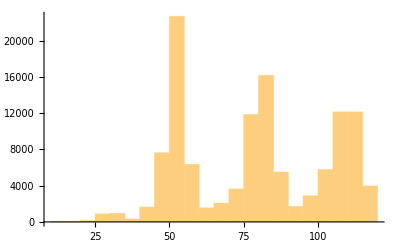

119

32

```mathematica
StringSplit/@data1$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

### Tokenize split data from the sampled polynomials

```mathematica
Get["MMA2TxtFormat3.m"];
Generate$data2$format3[n_]:=Monitor[Flatten[Table[
{longExpand,longSplit,short,sub}=data1and2$CommonSet⟦i⟧;
expandedForm=MMAExprToJFString[longExpand]<>" ? "<>MMAExprToJFString[sub];
splitForm=MMAExprToJFStringNonExpand[longSplit]<>" ? "<>MMAExprToJFString[sub];
{expandedForm,splitForm},{i,n}],1],Row[{"Generating element: ",i}]]
```

```mathematica
data2$format3=Generate$data2$format3[50000];
Length[data2$format3]
```

100000

```mathematica
data2$format3⟦1;;2⟧
```

{+ P 2 1 + * P 1 2 0 a1 + * P 1 2 4 ^ a1 P 2 + * N 4 8 ^ a1 P 3 * P 4 ^ a1 P 4 ? + N 2 + * N 6 a1 ^ a1 P 2,+ P 1 7 + P 4 + * P 1 2 0 a1 + * P 1 2 4 ^ a1 P 2 + * N 1 1 ^ a1 P 3 + * N 3 7 ^ a1 P 3 + * P 3 ^ a1 P 4 ^ a1 P 4 ? + N 2 + * N 6 a1 ^ a1 P 2}

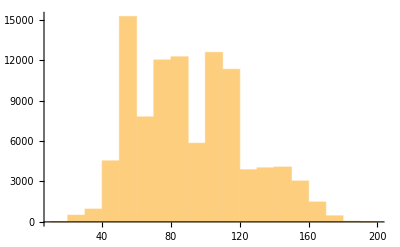

195

32

```mathematica
StringSplit/@data2$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

### Save dataset

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/repos/PolynomialSubstructure/MMA_package

```mathematica
Export["data_storage/dataset/example_single/single_variable_test.txt",data1$format3⟦1;;3000⟧,"Text"]
Export["data_storage/dataset/example_single/single_variable_valid.txt",data1$format3⟦3001;;3128⟧,"Text"]
Export["data_storage/dataset/example_single/nonsplit_data_train.txt",data1$format3⟦3129;;103128⟧,"Text"]
Export["data_storage/dataset/example_single/split_data_train.txt",data2$format3⟦1;;100000⟧,"Text"]
```

data_storage/dataset/example_single/single_variable_test.txt

data_storage/dataset/example_single/single_variable_valid.txt

data_storage/dataset/example_single/nonsplit_data_train.txt

data_storage/dataset/example_single/split_data_train.txt

## Generating O(N) dataset

### Sample polynomials with O(N) singlet substructure

```mathematica
(* original expression has max coefficient 10 and max degree 2 *)
(* substitution is possible O(2) singlet from 10 vectors *)
```

```mathematica
GenerateTrainSet$ON$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$ON$LSS2[10,2,2,10,ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$ON$CommonSet[5]//TableForm
```

-7-2 a[11] a[13]-36 a[11]^2 a[13]^2-2 a[12] a[14]-72 a[11] a[12] a[13] a[14]-36 a[12]^2 a[14]^2-2 a[13] a[15]-72 a[11] a[13]^2 a[15]-72 a[12] a[13] a[14] a[15]-36 a[13]^2 a[15]^2-2 a[14] a[16]-72 a[11] a[13] a[14] a[16]-72 a[12] a[14]^2 a[16]-72 a[13] a[14] a[15] a[16]-36 a[14]^2 a[16]^2 | -7+s-9 s^2 | -2 (a[11] a[13]+a[12] a[14])-2 a[13] a[15]-2 a[14] a[16]
6+14 a[3] a[5]+24 a[3]^2 a[5]^2+14 a[4] a[6]+48 a[3] a[4] a[5] a[6]+24 a[4]^2 a[6]^2-28 a[1] a[7]-96 a[1] a[3] a[5] a[7]-96 a[1] a[4] a[6] a[7]+96 a[1]^2 a[7]^2-28 a[2] a[8]-96 a[2] a[3] a[5] a[8]-96 a[2] a[4] a[6] a[8]+192 a[1] a[2] a[7] a[8]+96 a[2]^2 a[8]^2 | 6+7 s+6 s^2 | 2 (a[3] a[5]+a[4] a[6])-4 (a[1] a[7]+a[2] a[8])
-1+24 a[11] a[15]-96 a[11]^2 a[15]^2+24 a[12] a[16]-192 a[11] a[12] a[15] a[16]-96 a[12]^2 a[16]^2-18 a[3] a[17]+144 a[3] a[11] a[15] a[17]+144 a[3] a[12] a[16] a[17]-54 a[3]^2 a[17]^2-18 a[4] a[18]+144 a[4] a[11] a[15] a[18]+144 a[4] a[12] a[16] a[18]-108 a[3] a[4] a[17] a[18]-54 a[4]^2 a[18]^2+18 a[13] a[19]-144 a[11] a[13] a[15] a[19]-144 a[12] a[13] a[16] a[19]+108 a[3] a[13] a[17] a[19]+108 a[4] a[13] a[18] a[19]-54 a[13]^2 a[19]^2+18 a[14] a[20]-144 a[11] a[14] a[15] a[20]-144 a[12] a[14] a[16] a[20]+108 a[3] a[14] a[17] a[20]+108 a[4] a[14] a[18] a[20]-108 a[13] a[14] a[19] a[20]-54 a[14]^2 a[20]^2 | -1-6 s-6 s^2 | -4 (a[11] a[15]+a[12] a[16])+3 (a[3] a[17]+a[4] a[18])-3 (a[13] a[19]+a[14] a[20])
-9-7 a[3] a[9]-5 a[3]^2 a[9]^2-7 a[4] a[10]-10 a[3] a[4] a[9] a[10]-5 a[4]^2 a[10]^2+28 a[1] a[11]+28 a[5] a[11]+40 a[1] a[3] a[9] a[11]+40 a[3] a[5] a[9] a[11]+40 a[1] a[4] a[10] a[11]+40 a[4] a[5] a[10] a[11]-80 a[1]^2 a[11]^2-160 a[1] a[5] a[11]^2-80 a[5]^2 a[11]^2+28 a[2] a[12]+28 a[6] a[12]+40 a[2] a[3] a[9] a[12]+40 a[3] a[6] a[9] a[12]+40 a[2] a[4] a[10] a[12]+40 a[4] a[6] a[10] a[12]-160 a[1] a[2] a[11] a[12]-160 a[2] a[5] a[11] a[12]-160 a[1] a[6] a[11] a[12]-160 a[5] a[6] a[11] a[12]-80 a[2]^2 a[12]^2-160 a[2] a[6] a[12]^2-80 a[6]^2 a[12]^2 | -9-7 s-5 s^2 | a[3] a[9]+a[4] a[10]-4 (a[1] a[11]+a[2] a[12])-4 (a[5] a[11]+a[6] a[12])
6-12 a[1] a[15]+36 a[1]^2 a[15]^2-12 a[2] a[16]+72 a[1] a[2] a[15] a[16]+36 a[2]^2 a[16]^2+8 a[9] a[19]-48 a[1] a[9] a[15] a[19]-48 a[2] a[9] a[16] a[19]+16 a[9]^2 a[19]^2+8 a[10] a[20]-48 a[1] a[10] a[15] a[20]-48 a[2] a[10] a[16] a[20]+32 a[9] a[10] a[19] a[20]+16 a[10]^2 a[20]^2 | 6-4 s+4 s^2 | 3 (a[1] a[15]+a[2] a[16])-2 (a[9] a[19]+a[10] a[20])

```mathematica
TrainSet$ON$CommonSet = GenerateTrainSet$ON$CommonSet[110000];
```

```mathematica
TrainSet$ON$CommonSet = DeleteDuplicatesBy[TrainSet$ON$CommonSet,First];
Length[TrainSet$ON$CommonSet]
```

109994

### Tokenize polynomials

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
GenerateTrainSet$ON$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$ON$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
GenerateTrainSet$ON$format3[2]
```

{+ N 1 0 + * P 4 0 * a3 a11 + * N 1 2 8 * ^ a3 P 2 ^ a11 P 2 + * P 4 0 * a4 a12 + * N 2 5 6 * a3 * a4 * a11 a12 + * N 1 2 8 * ^ a4 P 2 ^ a12 P 2 + * P 4 0 * a9 a17 + * N 2 5 6 * a3 * a9 * a11 a17 + * N 2 5 6 * a4 * a9 * a12 a17 + * N 1 2 8 * ^ a9 P 2 ^ a17 P 2 + * P 4 0 * a10 a18 + * N 2 5 6 * a3 * a10 * a11 a18 + * N 2 5 6 * a4 * a10 * a12 a18 + * N 2 5 6 * a9 * a10 * a17 a18 + * N 1 2 8 * ^ a10 P 2 ^ a18 P 2 + * N 1 0 * a7 a19 + * P 6 4 * a3 * a7 * a11 a19 + * P 6 4 * a4 * a7 * a12 a19 + * P 6 4 * a7 * a9 * a17 a19 + * P 6 4 * a7 * a10 * a18 a19 + * N 8 * ^ a7 P 2 ^ a19 P 2 + * N 1 0 * a8 a20 + * P 6 4 * a3 * a8 * a11 a20 + * P 6 4 * a4 * a8 * a12 a20 + * P 6 4 * a8 * a9 * a17 a20 + * P 6 4 * a8 * a10 * a18 a20 + * N 1 6 * a7 * a8 * a19 a20 * N 8 * ^ a8 P 2 ^ a20 P 2 ? + * P 4 + * a3 a11 * a4 a12 + * P 4 + * a9 a17 * a10 a18 + * N 1 * a7 a19 * N 1 * a8 a20,+ N 1 + * N 2 7 * a1 a3 + * P 5 4 * ^ a1 P 2 ^ a3 P 2 + * N 2 7 * a2 a4 + * P 1 0 8 * a1 * a2 * a3 a4 + * P 5 4 * ^ a2 P 2 ^ a4 P 2 + * P 1 8 * a5 a9 + * N 7 2 * a1 * a3 * a5 a9 + * N 7 2 * a2 * a4 * a5 a9 + * P 2 4 * ^ a5 P 2 ^ a9 P 2 + * P 1 8 * a6 a10 + * N 7 2 * a1 * a3 * a6 a10 + * N 7 2 * a2 * a4 * a6 a10 + * P 4 8 * a5 * a6 * a9 a10 + * P 2 4 * ^ a6 P 2 ^ a10 P 2 + * P 4 5 * a9 a11 + * N 1 8 0 * a1 * a3 * a9 a11 + * N 1 8 0 * a2 * a4 * a9 a11 + * P 1 2 0 * a5 * ^ a9 P 2 a11 + * P 1 2 0 * a6 * a9 * a10 a11 + * P 1 5 0 * ^ a9 P 2 ^ a11 P 2 + * P 4 5 * a10 a12 + * N 1 8 0 * a1 * a3 * a10 a12 + * N 1 8 0 * a2 * a4 * a10 a12 + * P 1 2 0 * a5 * a9 * a10 a12 + * P 1 2 0 * a6 * ^ a10 P 2 a12 + * P 3 0 0 * a9 * a10 * a11 a12 * P 1 5 0 * ^ a10 P 2 ^ a12 P 2 ? + * N 3 + * a1 a3 * a2 a4 + * P 2 + * a5 a9 * a6 a10 * P 5 + * a9 a11 * a10 a12}

```mathematica
TrainSet$ON$format3=GenerateTrainSet$ON$format3[100000];
```

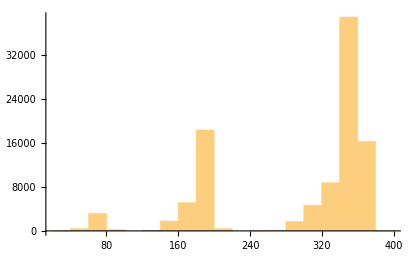

380

45

```mathematica
StringSplit/@TrainSet$ON$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

### Save dataset

```mathematica
SetDirectory[NotebookDirectory[]]
Export["data_storage/dataset/example_ON/ON_data_valid.txt",TrainSet$ON$format3⟦1;;128⟧,"Text"]
Export["data_storage/dataset/example_ON/ON_data_test.txt",TrainSet$ON$format3⟦129;;3128⟧,"Text"]
Export["data_storage/dataset/example_ON/ON_data_train.txt",TrainSet$ON$format3⟦3129;;100000⟧,"Text"]
```

/Users/jaeha/repos/PolynomialSubstructure/MMA_package

data_storage/dataset/example_ON/ON_data_valid.txt

data_storage/dataset/example_ON/ON_data_test.txt

data_storage/dataset/example_ON/ON_data_train.txt

## Generating multi variable dataset

### Sample multi variable polynomials

```mathematica
(* original expression: degree 3 terms with maximum coefficient 5, maximum 3 terms *)
(* substitution: degree 3 terms with maximum coefficient 5, maximum 3 terms *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$multi$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
(* examples *)
```

```mathematica
GenerateTrainSet$multi$CommonSet[3]//TableForm
```

-24 a[1]^9-108 a[0] a[1]^6 a[2]^2+64 a[1]^6 a[2]^3-162 a[0]^2 a[1]^3 a[2]^4-81 a[0]^3 a[2]^6 | -3 b[0]^3+b[1]^3 | 2 a[1]^3+3 a[0] a[2]^2 | 4 a[1]^2 a[2]
-192 a[0]^6 a[2]^3-20 a[0]^2 a[1]^4 a[2]^3+3 a[1]^6 a[2]^3-120 a[0]^3 a[1]^2 a[2]^4+27 a[0] a[1]^4 a[2]^4-180 a[0]^4 a[2]^5+81 a[0]^2 a[1]^2 a[2]^5+81 a[0]^3 a[2]^6 | 3 b[0]^3+5 b[0]^2 b[1]+3 b[1]^3 | a[1]^2 a[2]+3 a[0] a[2]^2 | -4 a[0]^2 a[2]
-90 a[0]^5 a[1]^3 a[2]-195 a[0]^4 a[1]^3 a[2]^2-420 a[0]^3 a[1]^3 a[2]^3-990 a[0]^2 a[1]^3 a[2]^4-1050 a[0] a[1]^3 a[2]^5-375 a[1]^3 a[2]^6 | 2 b[0]^2 b[1]+b[0] b[1]^2+3 b[1]^3 | 3 a[0]^2 a[1]+3 a[0] a[1] a[2] | -5 a[0] a[1] a[2]-5 a[1] a[2]^2

```mathematica
(* sample polynomials *)
```

```mathematica
TrainSet$multi$CommonSet = GenerateTrainSet$multi$CommonSet[110000];
```

```mathematica
TrainSet$multi$CommonSet = DeleteDuplicatesBy[TrainSet$multi$CommonSet,First];
Length[TrainSet$multi$CommonSet]
```

### Tokenize polynomials

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
GenerateTrainSet$multi$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2}=TrainSet$multi$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2];
{original}],{i,Min[n,Length[TrainSet$multi$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
GenerateTrainSet$multi$CommonSet$format3[3]//TableForm
```

+ * P 5 4 * ^ a0 P 5 * a1 ^ a2 P 3 + * N 1 5 3 * ^ a0 P 4 * ^ a1 P 2 ^ a2 P 3 + * P 5 1 * ^ a0 P 3 * ^ a1 P 3 ^ a2 P 3 + * N 5 4 * ^ a0 P 5 ^ a2 P 4 + * P 1 2 6 * ^ a0 P 4 * a1 ^ a2 P 4 + * P 1 0 2 * ^ a0 P 3 * ^ a1 P 2 ^ a2 P 4 + * P 2 7 * ^ a0 P 4 ^ a2 P 5 + * N 2 0 7 * ^ a0 P 3 * a1 ^ a2 P 5 * P 5 4 * ^ a0 P 3 ^ a2 P 6 ? + * P 2 * ^ b0 P 2 b1 + * N 1 * b0 ^ b1 P 2 * N 2 ^ b1 P 3 & + * N 3 * ^ a0 P 2 a2 * P 5 * a0 * a1 a2 & + * P 3 * a0 * a1 a2 * N 3 * a0 ^ a2 P 2
+ * N 2 7 * ^ a0 P 3 ^ a1 P 6 + * N 5 4 * ^ a0 P 2 ^ a1 P 7 + * N 3 6 * a0 ^ a1 P 8 + * N 1 1 6 ^ a1 P 9 + * P 2 1 6 * ^ a0 P 2 * ^ a1 P 6 a2 + * N 1 4 4 * ^ a0 P 4 * ^ a1 P 3 ^ a2 P 2 * P 3 2 * ^ a0 P 6 ^ a2 P 3 ? + * N 1 ^ b0 P 3 * P 4 ^ b1 P 3 & + * P 3 * a0 ^ a1 P 2 * P 2 ^ a1 P 3 & + * N 3 ^ a1 P 3 * P 2 * ^ a0 P 2 a2
+ * N 4 ^ a1 P 9 * P 3 * ^ a1 P 8 a2 ? + * N 4 ^ b0 P 3 * P 3 * ^ b0 P 2 b1 & ^ a1 P 3 & * ^ a1 P 2 a2

```mathematica
TrainSet$multi$format3=GenerateTrainSet$multi$CommonSet$format3[108000];
Length[TrainSet$multi$format3]
```

108000

```mathematica
(* dataset information *)
```

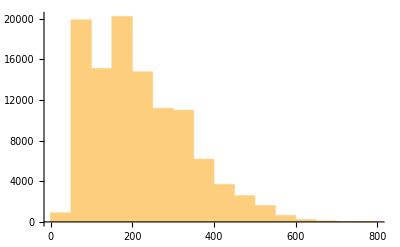

765

87

```mathematica
StringSplit/@TrainSet$multi$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

### Save dataset

```mathematica
SetDirectory[NotebookDirectory[]]
Export["data_storage/dataset/example_multi/multi_data_valid.txt",TrainSet$multi$format3⟦1;;128⟧,"Text"]
Export["data_storage/dataset/example_multi/multi_data_test.txt",TrainSet$multi$format3⟦129;;3128⟧,"Text"]
Export["data_storage/dataset/example_multi/multi_data_train.txt",TrainSet$multi$format3⟦3129;;100000⟧,"Text"]
```

/Users/jaeha/repos/PolynomialSubstructure/MMA_package

data_storage/dataset/example_multi/multi_data_valid.txt

data_storage/dataset/example_multi/multi_data_test.txt

data_storage/dataset/example_multi/multi_data_train.txt

## evaluate result

### ~ Exp 53

#### Example of usage ( Exp33 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp33/test_set_Exp14.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp33/experiment33_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
testdata[[1;;3]]
```

{{1700-165 a[1]+4 a[1]^2,-20+a[1]},{-51+3 a[1],-17+a[1]},{-8-60 a[1]-94 a[1]^2+20 a[1]^3-a[1]^4,-2-10 a[1]+a[1]^2}}

```mathematica
predictiondata[[1;;3]]
```

{-20+a[1],-17+a[1],-4-10 a[1]+a[1]^2}

```mathematica
simplification$result=Table[PolySimplifyWithHint[{testdata[[i,1]],predictiondata[[i]]},False,True],{i,1,Length@predictiondata}];
```

```mathematica
simplification$result[[1;;3]]
```

{-5 s+4 s^2,3 s,-2 s-s^2}

```mathematica
(* percentage of grammatic error *)
pctg$grammaticerr=Count[predictiondata,False]/Length[predictiondata]//N
```

0.000666667

```mathematica
(* percentage of wrong cases, excluding grammatic error *)
pctg$wrong=Count[simplification$result,False]/Length[simplification$result]-pctg$grammaticerr//N
```

0.00766667

```mathematica
(* percentage of correct cases*)
pctg$correct=1-Count[simplification$result,False]/Length[simplification$result]//N
```

0.991667

```mathematica
(* package above code into a function *)
EvaluateSimplificationResult[testfile_,predictionfile_,complexityCriteriaQ_:True,eliminateQ_:True]:=Module[
{testdata,predictiondata,simplification$result,pctg$grammaticerr,pctg$wrong,pctg$correct},
testdata=TestData$FromFile[testfile];
predictiondata=PredictionData$FromFile[predictionfile];
simplification$result=Table[PolySimplifyWithHint[{testdata[[i,1]],predictiondata[[i]]},complexityCriteriaQ,eliminateQ],{i,1,Length@predictiondata}];

pctg$grammaticerr=Count[predictiondata,False]/Length[predictiondata]//N;
pctg$wrong=Count[simplification$result,False]/Length[simplification$result]-pctg$grammaticerr//N;
pctg$correct=1-Count[simplification$result,False]/Length[simplification$result]//N;

{pctg$grammaticerr,pctg$wrong,pctg$correct}
];
```

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
EvaluateSimplificationResult["./Evaluation/Exp33/test_set_Exp14.txt","./Evaluation/Exp33/experiment33_predictions.txt",False,True]
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.000666667,0.00766667,0.991667}

#### Test model from Exp33 on contaminated data (test1)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp33_test1/IndecomposableTest_Test1_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp33_test1/experiment33_indecomposable_test1_predictions.txt"];
```

```mathematica
EvaluateSimplificationResult["./Evaluation/Exp33_test1/IndecomposableTest_Test1_Format3.txt","./Evaluation/Exp33_test1/experiment33_indecomposable_test1_predictions.txt"]
```

{0.,0.04,0.96}

```mathematica
testdata⟦2⟧
predictiondata⟦2⟧
```

{297+308 a[1]-1383 a[1]^2-683 a[1]^3+1845 a[1]^4-190 a[1]^5+5 a[1]^6,8+4 a[1]-19 a[1]^2+a[1]^3}

9+4 a[1]-19 a[1]^2+a[1]^3

```mathematica
PolySimplifyWithHint[{testdata[[2,1]],8+4 a[1]-19 a[1]^2+a[1]^3},False,True]
```

1-3 s+5 s^2

#### Test model from Exp33 on contaminated data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp33_test2/IndecomposableTest_Test2_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp33_test2/experiment33_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
EvaluateSimplificationResult["./Evaluation/Exp33_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp33_test2/experiment33_indecomposable_test2_predictions.txt"]
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.001,0.731333,0.267667}

```mathematica
EvaluateSimplificationResult["./Evaluation/Exp33_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp33_test2/experiment33_indecomposable_test2_predictions.txt",True,False]
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.001,0.506,0.493}

#### Test model from Exp34 on non contaminated data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp34/test_set_Exp34.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp34/experiment34_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp34/test_set_Exp34.txt","./Evaluation/Exp34/experiment34_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
```

{0.298333,0.0303333,0.671333}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp34/test_set_Exp34.txt","./Evaluation/Exp34/experiment34_predictions.txt",True,False];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result2
```

{0.298333,0.0493333,0.652333}

#### Test model from Exp34 on contaminated data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp34_test2/IndecomposableTest_Test2_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp34_test2/experiment34_indecomposable_test2_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp34_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp34_test2/experiment34_indecomposable_test2_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

```mathematica
result1
```

{0.115667,0.634,0.250333}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp34_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp34_test2/experiment34_indecomposable_test2_predictions.txt",True,False];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

```mathematica
result2
```

{0.115667,0.703333,0.181}

#### Test model from Exp37 on non contaminated data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp37/test_set_Exp36.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp37/experiment37_predictions.txt"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp37/test_set_Exp36.txt","./Evaluation/Exp37/experiment37_predictions.txt"];
```

```mathematica
result1
```

{0.,0.0113333,0.988667}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp37/test_set_Exp36.txt","./Evaluation/Exp37/experiment37_predictions.txt",True,False];
```

```mathematica
result2
```

{0.,0.011,0.989}

#### Test model from Exp37 on contaminated data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp37_test2/IndecomposableTest_Test2_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp37_test2/experiment37_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp37_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp37_test2/experiment37_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1
```

{0.0136667,0.984667,0.00166667}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp37_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp37_test2/experiment37_indecomposable_test2_predictions.txt",True,False];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result2
```

{0.0136667,0.501,0.485333}

#### Random suggestion benchmark

```mathematica
testdata⟦1⟧
predictiondata⟦1⟧
```

{480-97 a[1]+1867 a[1]^2-876 a[1]^3+1777 a[1]^4-1320 a[1]^5+55 a[1]^6+70 a[1]^7+5 a[1]^8,-10+a[1]-19 a[1]^2+7 a[1]^3+a[1]^4}

-10+a[1]-19 a[1]^2+7 a[1]^3+a[1]^4

```mathematica
predictiondata[[9]]
```

6+a[1]

```mathematica
i0=16;predictiondata[[i0]]
PolySimplifyWithHint[{testdata[[1,1]],predictiondata[[i0]]},False,True]
PolySimplifyWithHint[{testdata[[1,1]],predictiondata[[i0]]},True,False]
```

-12-13 a[1]+6 a[1]^2-11 a[1]^3+a[1]^4

False

False

```mathematica
simplification$result$random=Table[PolySimplifyWithHint[{testdata[[1,1]],predictiondata[[i]]},False,True],{i,1,Length@predictiondata}];
pctg$correct$random=1-Count[simplification$result$random,False]/Length[simplification$result$random]/1.
simplification$result$random=Table[PolySimplifyWithHint[{testdata[[1,1]],predictiondata[[i]]},True,False],{i,1,Length@predictiondata}];
pctg$correct$random=1-Count[simplification$result$random,False]/Length[simplification$result$random]/1.
```

0.224667

0.000333333

#### Test model from Exp38 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp38/test_set_Exp38.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp38/experiment38_predictions.txt"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp38/test_set_Exp38.txt","./Evaluation/Exp38/experiment38_predictions.txt"];
```

```mathematica
result1
```

{0.,1.,0.}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp38/test_set_Exp38.txt","./Evaluation/Exp38/experiment38_predictions.txt",True,False];
```

```mathematica
result2
```

{0.,0.920333,0.0796667}

#### Test model from Exp38 on contaminated data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp38_test2/IndecomposableTest_Test2_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp38_test2/experiment38_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«6 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp38_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp38_test2/experiment38_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«6 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1
```

{0.044,0.956,0.}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp38_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp38_test2/experiment38_indecomposable_test2_predictions.txt",True,False];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«6 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result2
```

{0.044,0.303,0.653}

#### Test model from Exp38 on decomposable data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp38_test0/test_set_Exp14.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp38_test0/experiment38_decomposable_test_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp38_test0/test_set_Exp14.txt","./Evaluation/Exp38_test0/experiment38_decomposable_test_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
```

{0.039,0.297,0.664}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp38_test0/test_set_Exp14.txt","./Evaluation/Exp38_test0/experiment38_decomposable_test_predictions.txt",True,False];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result2
```

{0.039,0.294667,0.666333}

#### Test model from Exp39 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp39/test_set_Exp39.txt","./Evaluation/Exp39/experiment39_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
result1
```

{0.000333333,0.126667,0.873}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp39/test_set_Exp39.txt","./Evaluation/Exp39/experiment39_predictions.txt",True,False];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
result2
```

{0.000333333,0.00366667,0.996}

#### Test model from Exp40 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp40/test_set_Exp39.txt","./Evaluation/Exp40/experiment40_predictions.txt"];
```

```mathematica
result1
```

{0.,0.0376667,0.962333}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp40/test_set_Exp39.txt","./Evaluation/Exp40/experiment40_predictions.txt",True,False];
```

```mathematica
result2
```

{0.,0.001,0.999}

#### Test model from Exp41 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp41/test_set_Exp41.txt","./Evaluation/Exp41/experiment41_predictions.txt"];
```

```mathematica
result1
```

{0.,0.001,0.999}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp41/test_set_Exp41.txt","./Evaluation/Exp41/experiment41_predictions.txt",True,False];
```

```mathematica
result2
```

{0.,0.000333333,0.999667}

#### Test model from Exp44 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult2["./Evaluation/Exp44/test_set_Exp44.txt","./Evaluation/Exp44/experiment44_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
result
```

{0.,0.00633333,0.993667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp44/test_set_Exp44.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/Exp44/experiment44_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
index=132;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.b[0]->%⟦1⟧//Expand
```

6+21 a[1]^2 a[2]+9 a[1]^4 a[2]^2+56 a[1] a[2] a[3]+48 a[1]^3 a[2]^2 a[3]+64 a[1]^2 a[2]^2 a[3]^2

{3 a[1]^2 a[2]+8 a[1] a[2] a[3],6+7 b[0]+b[0]^2}

6+21 a[1]^2 a[2]+9 a[1]^4 a[2]^2+56 a[1] a[2] a[3]+48 a[1]^3 a[2]^2 a[3]+64 a[1]^2 a[2]^2 a[3]^2

#### Test model from Exp45 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp45/test_set_Exp45.txt","./Evaluation/Exp45/experiment45_predictions.txt"];
```

```mathematica
result
```

{0.,0.296333,0.703667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp45/test_set_Exp45.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp45/experiment45_predictions.txt"];
```

```mathematica
index=94;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

{{-5 a[2]-4 a[1] a[2]+2 a[1] a[3],2 a[1]},4 b[0]^2+4 b[0] b[1]+5 b[1]^2}

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

0

#### Test model from Exp46 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp46/test_set_Exp45.txt","./Evaluation/Exp46/experiment46_predictions.txt"];
```

```mathematica
result
```

{0.,0.632,0.368}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp46/test_set_Exp45.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp46/experiment46_predictions.txt"];
```

```mathematica
index=94;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

{{-2 a[1],-5 a[2]-4 a[1] a[2]-2 a[1] a[3]},5 b[0]^2-4 b[0] b[1]+4 b[1]^2}

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2-16 a[1]^2 a[3]+80 a[1] a[2] a[3]+64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

32 a[1]^2 a[3]-160 a[1] a[2] a[3]-128 a[1]^2 a[2] a[3]

#### Test model from Exp47 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp47/test_set_Exp45.txt","./Evaluation/Exp47/experiment47_predictions.txt"];
```

```mathematica
result
```

{0.,0.244333,0.755667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp46/test_set_Exp45.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp47/experiment47_predictions.txt"];
```

```mathematica
index=94;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

{{-5 a[2]-4 a[1] a[2]+2 a[1] a[3],2 a[1]},4 b[0]^2+4 b[0] b[1]+5 b[1]^2}

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

0

#### Test model from Exp50 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp50/test_set_Exp50.txt","./Evaluation/Exp50/experiment50_predictions.txt"];
```

```mathematica
result
```

{0.,0.809667,0.190333}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp50/test_set_Exp50.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp50/experiment50_predictions.txt"];
```

```mathematica
index=97;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

4 a[3]^2 a[4]^2-12 a[3] a[4]^3+9 a[4]^4+4 a[3] a[4] a[5] a[6]-6 a[4]^2 a[5] a[6]-6 a[3] a[4] a[6]^2+9 a[4]^2 a[6]^2-6 a[3] a[4] a[5] a[7]+9 a[4]^2 a[5] a[7]+2 a[3] a[4] a[6] a[7]-3 a[4]^2 a[6] a[7]

{{-2 a[3] a[4]+3 a[4]^2,2 a[5] a[6]+3 a[6]^2+3 a[5] a[7]-a[6] a[7]},b[0]^2+b[0] b[1]}

4 a[3]^2 a[4]^2-12 a[3] a[4]^3+9 a[4]^4-4 a[3] a[4] a[5] a[6]+6 a[4]^2 a[5] a[6]-6 a[3] a[4] a[6]^2+9 a[4]^2 a[6]^2-6 a[3] a[4] a[5] a[7]+9 a[4]^2 a[5] a[7]+2 a[3] a[4] a[6] a[7]-3 a[4]^2 a[6] a[7]

8 a[3] a[4] a[5] a[6]-12 a[4]^2 a[5] a[6]

#### Test model from Exp48 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp48/test_set_Exp48.txt","./Evaluation/Exp48/experiment48_predictions.txt"];
```

```mathematica
result
```

{0.476667,0.,0.794333,0.205667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp48/test_set_Exp48.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp48/experiment48_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1427 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«16 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«20 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«20 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«17 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«21 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«26 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«14 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«16 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«14 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«14 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
index=100;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

False

{{4 a[1]^2,-3 a[0] a[1]},False}

False

0

#### Test model from Exp52 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp52/test_set_Exp52.txt","./Evaluation/Exp52/experiment52_predictions.txt"];
```

```mathematica
result
```

{0.,0.,0.532333,0.467667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp52/test_set_Exp52.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp52/experiment52_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«16 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«17 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«24 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«24 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

```mathematica
index=9;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}
%%%-%//Expand
```

0

{{0,-5 a[0]-a[1]^2},False}

False

-False

#### Test model from Exp53 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp53/test_set_Exp53.txt","./Evaluation/Exp53/experiment53_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.,0.499333,0.500667}

#### Test model from Exp58 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp58/test_set_Exp58.txt","./Evaluation/Exp58/experiment58_predictions.txt"];
```

```mathematica
result
```

{0.,0.115,0.702,0.183,{False,False,False,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,True,False,True,False,True,True,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,True,True,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,True,False,False,True,False,True,True,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,True,True,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,True,True,True,False,True,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,True,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False,False,False,True,True,False,False,False,False,True,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,True,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,True,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,True,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,False,False,True,True,False,True,True,True,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,True,False,True,True,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,True,True,False,False,False,False,False,False,True,False,False,False,False,True,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,True,True,False,True,False,False,True,False,False,False,False,False,True,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,True,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,True,True,False,False,True,True,False,False,False,False,False,True,True,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False,False,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,True,False,False,True,True,True,False,False,False,False,True,False,False,True,True,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,True,True,False,True,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,True,False,False,True,False,False,False,False,False,False,True,True,False,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,True,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,True,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,True,True,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,True,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,True,True,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,True,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,True,False,False,True,True,False,False,False,True,False,False,False,True,False,False,False,False,True,True,True,True,False,False,False,True,True,False,False,True,False,False,True,False,False,False,False,False,True,True,True,True,True,True,False,False,False,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,True,False,True,True,False,False,False,False,True,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,True,True,False,False,False,False,False,False,True,True,False,False,False,False,False,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,True,False,False,True,True,False,True,True,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,True,True,False,False,False,True,False,False,False,False,False,False,True,True,True,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,True,True,True,False,False,True,True,False,True,False,False,False,False,True,False,False,False,False,True,False,False,True,True,False,False,False,True,True,False,False,False,True,False,False,True,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,True,False,True,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,True,False,False,False,False,True,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,True,False,False,False,True,True,False,True,False,False,True,True,False,False,True,False,False,False,False,False,False,True,False,False,True,False,False,False,True,False,False,False,True,True,True,False,False,False,False,False,True,False,False,False,False,False,False,True,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False}}

### generalization evaluation

#### with pad on 0th token, move one pad

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp33/test_set_Exp14.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp32_test/experiment32_test_predictions.txt"];
```

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
EvaluateSimplificationResult["./Evaluation/Exp33/test_set_Exp14.txt","./Evaluation/Exp32_test/experiment32_test_predictions.txt",False,True]
```

{0.,0.013,0.987}

#### Test model from Exp52, 53 on Exp45 test data (generalization 0)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/gen0/gen0_test_Exp45.txt","./Evaluation/gen0/experiment52_onExp45_predictions.txt"];
```

```mathematica
result
```

{0.,0.,0.396667,0.603333}

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/gen0/gen0_test_Exp45.txt","./Evaluation/gen0/experiment53_onExp45_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.,0.962667,0.0373333}

```mathematica
testdata=TestData$FromFile2["./Evaluation/gen0/gen0_test_Exp45.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/gen0/experiment53_onExp45_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
index=921;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

-8 a[0]^2+48 a[0]^4-3 a[1]+5 a[0] a[1]+72 a[0]^2 a[1]+27 a[1]^2

{{-4 a[0]^2-3 a[1],-2 a[0]^2-5 a[1]},4 b[0]+3 b[0]^2-2 b[0] b[1]}

-16 a[0]^2+32 a[0]^4-12 a[1]+20 a[0]^2 a[1]-3 a[1]^2

8 a[0]^2+16 a[0]^4+9 a[1]+5 a[0] a[1]+52 a[0]^2 a[1]+30 a[1]^2

#### Generalization test on Exp45 model ( generalization 1, 2 )

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/gen1/gen1_test_Exp45.txt","./Evaluation/gen1/gen1_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.,0.944,0.056}

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/gen2/gen2_test_Exp45.txt","./Evaluation/gen2/gen2_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.,0.966,0.034}

#### Generalization test on Exp33 model ( benchmark, gen3, gen4, real_benchmark, gen5, gen6 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen3/benchmark.txt","./Evaluation/gen3/experiment33_check_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«28 more identical outputs»

```mathematica
result
```

{0.,0.738,0.262}

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen3/gen3_test.txt","./Evaluation/gen3/experiment33_gen3_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

```mathematica
result
```

{0.,0.818,0.182}

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen4/gen4_test.txt","./Evaluation/gen4/experiment33_gen4_predictions.txt",False,True];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«13 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«7 more identical outputs»

```mathematica
result
```

{0.,0.825667,0.174333}

```mathematica
testdata=TestData$FromFile["./Evaluation/gen4/gen4_test.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/gen4/experiment33_gen4_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«13 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«7 more identical outputs»

```mathematica
index=17;
testdata⟦index⟧
predictiondata⟦index⟧
PolySimplifyWithHint[{%%⟦1⟧,%},False,True]
%/.{s->%%⟦1⟧}//Expand
```

{1323-3402 a[1]+2187 a[1]^2,-21+27 a[1]}

{-19-6 a[1]+a[1]^2}

False

False

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen3/real_benchmark.txt","./Evaluation/gen3/experiment33_check2_predictions.txt",False,True];
```

```mathematica
result
```

{0.,0.00933333,0.990667}

```mathematica
result = EvaluateSimplificationResult["./Evaluation/gen5/gen5_test.txt","./Evaluation/gen5/experiment33_gen5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

```mathematica
result
```

{0.,0.818,0.182}

```mathematica
result = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/experiment33_gen6_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

{0.,0.741667,0.258333}

```mathematica
result
```

{0.,0.741667,0.258333}

#### Generalization test on Exp54 model ( real_benchmark, gen5, gen6 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen3/real_benchmark.txt","./Evaluation/gen3/experiment54_benchmark.txt",False,True];
```

```mathematica
result
```

{0.,0.004,0.996}

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen5/gen5_test.txt","./Evaluation/gen5/experiment54_gen5_predictions.txt",False,True];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

```mathematica
result
```

{0.,0.835667,0.164333}

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/experiment54_gen6_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.766667,0.233333}

```mathematica
testdata=TestData$FromFile["./Evaluation/gen5/gen5_test.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/gen5/experiment54_gen5_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

```mathematica
index=573;
testdata⟦index⟧
predictiondata⟦index⟧
PolySimplifyWithHint[{%%⟦1⟧,%},False,True]
%/.{s->%%⟦1⟧}//Expand
```

{-3851,20}

{-1799111119999999999999999999999999999999999999999}

True

True

#### Test model from Exp55_1,2 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp55/experiment55_1_predictions.txt"];
```

```mathematica
result⟦1;;4⟧
```

{0.,0.,0.201,0.799}

```mathematica
exp55$1result=result⟦5⟧;
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp55/experiment55_2_predictions.txt"];
```

```mathematica
result⟦1;;4⟧
```

{0.,0.,0.196,0.804}

```mathematica
exp55$2result=result⟦5⟧;
```

```mathematica
exp55results=Table[{exp55$1result⟦i⟧,exp55$2result⟦i⟧},{i,Length[exp55$1result]}];
```

```mathematica
{N[Count[exp55results,{False,False}]/Length[exp55results]],N[Count[exp55results,{False,True}]/Length[exp55results]],N[Count[exp55results,{True,False}]/Length[exp55results]],N[Count[exp55results,{True,True}]/Length[exp55results]]}
```

{0.153333,0.0476667,0.0426667,0.756333}

```mathematica
hardcases=Position[exp55results,{False,False}]//Flatten;
easycases=Position[exp55results,{True,True}]//Flatten;
middlecases=Position[exp55results,{True,False}|{False,True}]//Flatten;
```

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp55/test_set_Exp55.txt"];
testdataanswer=TestData$FromFile2$answers["./Evaluation/Exp55/test_set_Exp55.txt"];
predictiondata1=PredictionData$FromFile2["./Evaluation/Exp55/experiment55_1_predictions.txt"];
predictiondata2=PredictionData$FromFile2["./Evaluation/Exp55/experiment55_2_predictions.txt"];
```

```mathematica
Length[hardcases]
Length[easycases]
```

460

2269

```mathematica
LeafCount/@testdata⟦hardcases⟧//N//Mean
LeafCount/@testdata⟦easycases⟧//N//Mean
```

49.0565

32.6152

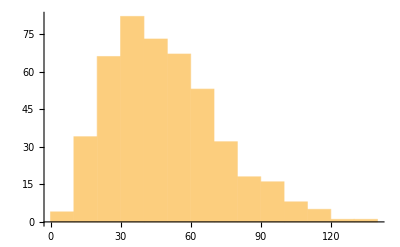

```mathematica
LeafCount/@testdata⟦hardcases⟧//Histogram
```

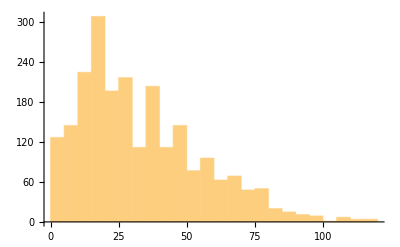

```mathematica
LeafCount/@testdata⟦easycases⟧//Histogram
```

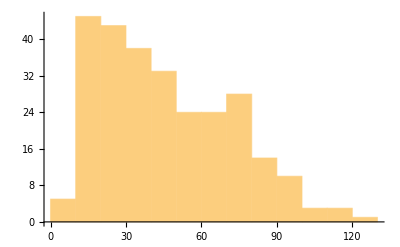

```mathematica
LeafCount/@testdata⟦middlecases⟧//Histogram
```

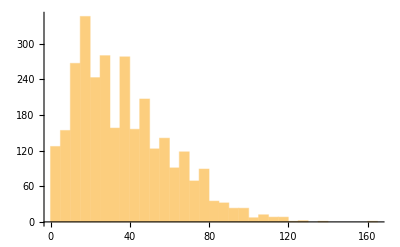

```mathematica
LeafCount/@testdata//Histogram
```

```mathematica
ii=409;
index = hardcases⟦ii⟧;
testdataanswer⟦index⟧
testdata⟦index⟧
predictiondata1⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand;
predictiondata2⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand;
```

{{2 a[2]+5 a[1] a[2]-4 a[2]^2,-5 a[1]^2+5 a[1] a[2]},-2 b[0]+5 b[0]^2+3 b[0] b[1]}

-4 a[2]-10 a[1] a[2]-30 a[1]^2 a[2]-75 a[1]^3 a[2]+28 a[2]^2+130 a[1] a[2]^2+260 a[1]^2 a[2]^2-80 a[2]^3-260 a[1] a[2]^3+80 a[2]^4

{{-2 a[2]-5 a[1] a[2]+4 a[2]^2,-3 a[1]^2+2 a[1] a[2]},2 b[0]+5 b[0]^2-5 b[0] b[1]}

-4 a[2]-10 a[1] a[2]-30 a[1]^2 a[2]-75 a[1]^3 a[2]+28 a[2]^2+120 a[1] a[2]^2+235 a[1]^2 a[2]^2-80 a[2]^3-240 a[1] a[2]^3+80 a[2]^4

{{-2 a[2]+5 a[1] a[2]+4 a[2]^2,-5 a[1]^2+5 a[1] a[2]},2 b[0]+5 b[0]^2-3 b[0] b[1]}

-4 a[2]+10 a[1] a[2]-30 a[1]^2 a[2]+75 a[1]^3 a[2]+28 a[2]^2-70 a[1] a[2]^2+110 a[1]^2 a[2]^2-80 a[2]^3+140 a[1] a[2]^3+80 a[2]^4

```mathematica
ii=59;
index = easycases⟦ii⟧;
testdataanswer⟦index⟧
testdata⟦index⟧
predictiondata1⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand;
%%%-%//Expand;
predictiondata2⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand;
%%%-%//Expand;
```

{{3 a[1]-5 a[1]^2-2 a[2] a[3],-5 a[3]},b[0]-2 b[1]-3 b[1]^2}

3 a[1]-5 a[1]^2+10 a[3]-2 a[2] a[3]-75 a[3]^2

{{-5 a[3],3 a[1]-5 a[1]^2-2 a[2] a[3]},-2 b[0]-3 b[0]^2+b[1]}

{{-5 a[3],3 a[1]-5 a[1]^2-2 a[2] a[3]},-2 b[0]-3 b[0]^2+b[1]}

#### further training on longer data (Exp56) comparing with Exp55_1,2

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp55/experiment55_1_predictions.txt"];
```

```mathematica
result⟦1;;4⟧
```

{0.,0.,0.201,0.799}

```mathematica
exp55$1result=result⟦5⟧;
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp55/experiment55_2_predictions.txt"];
```

```mathematica
result⟦1;;4⟧
```

{0.,0.,0.196,0.804}

```mathematica
exp55$2result=result⟦5⟧;
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp56/experiment56_predictions.txt"];
result⟦1;;4⟧
exp56$result=result⟦5⟧;
```

{0.,0.,0.179333,0.820667}

```mathematica
exp55results=Table[{exp55$1result⟦i⟧,exp55$2result⟦i⟧},{i,Length[exp55$1result]}];
```

```mathematica
{N[Count[exp55results,{False,False}]/Length[exp55results]],N[Count[exp55results,{False,True}]/Length[exp55results]],N[Count[exp55results,{True,False}]/Length[exp55results]],N[Count[exp55results,{True,True}]/Length[exp55results]]}
```

{0.153333,0.0476667,0.0426667,0.756333}

```mathematica
hardcases=Position[exp55results,{False,False}]//Flatten;
easycases=Position[exp55results,{True,True}]//Flatten;
middlecases=Position[exp55results,{True,False}|{False,True}]//Flatten;
```

```mathematica
exp56onhard = Table[exp56$result⟦hardcases⟦i⟧⟧,{i,Length[hardcases]}];
exp56oneasy = Table[exp56$result⟦easycases⟦i⟧⟧,{i,Length[easycases]}];
{N[Count[exp56onhard,True]/Length[exp56onhard]],N[Count[exp56oneasy,True]/Length[exp56oneasy]]}
```

{0.13913,0.981049}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp55/test_set_Exp55.txt"];
testdataanswer=TestData$FromFile2$answers["./Evaluation/Exp55/test_set_Exp55.txt"];
predictiondata1=PredictionData$FromFile2["./Evaluation/Exp55/experiment55_1_predictions.txt"];
predictiondata2=PredictionData$FromFile2["./Evaluation/Exp55/experiment55_2_predictions.txt"];
```

```mathematica
Length[hardcases]
Length[easycases]
```

460

2269

```mathematica
LeafCount/@testdata⟦hardcases⟧//N//Mean
LeafCount/@testdata⟦easycases⟧//N//Mean
```

49.0565

32.6152

```mathematica
LeafCount/@testdata⟦hardcases⟧//Histogram
```

-Graphics-

```mathematica
LeafCount/@testdata⟦easycases⟧//Histogram
```

-Graphics-

```mathematica
LeafCount/@testdata⟦middlecases⟧//Histogram
```

-Graphics-

```mathematica
LeafCount/@testdata//Histogram
```

-Graphics-

```mathematica
ii=409;
index = hardcases⟦ii⟧;
testdataanswer⟦index⟧
testdata⟦index⟧
predictiondata1⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand;
predictiondata2⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand;
```

{{2 a[2]+5 a[1] a[2]-4 a[2]^2,-5 a[1]^2+5 a[1] a[2]},-2 b[0]+5 b[0]^2+3 b[0] b[1]}

-4 a[2]-10 a[1] a[2]-30 a[1]^2 a[2]-75 a[1]^3 a[2]+28 a[2]^2+130 a[1] a[2]^2+260 a[1]^2 a[2]^2-80 a[2]^3-260 a[1] a[2]^3+80 a[2]^4

{{-2 a[2]-5 a[1] a[2]+4 a[2]^2,-3 a[1]^2+2 a[1] a[2]},2 b[0]+5 b[0]^2-5 b[0] b[1]}

-4 a[2]-10 a[1] a[2]-30 a[1]^2 a[2]-75 a[1]^3 a[2]+28 a[2]^2+120 a[1] a[2]^2+235 a[1]^2 a[2]^2-80 a[2]^3-240 a[1] a[2]^3+80 a[2]^4

{{-2 a[2]+5 a[1] a[2]+4 a[2]^2,-5 a[1]^2+5 a[1] a[2]},2 b[0]+5 b[0]^2-3 b[0] b[1]}

-4 a[2]+10 a[1] a[2]-30 a[1]^2 a[2]+75 a[1]^3 a[2]+28 a[2]^2-70 a[1] a[2]^2+110 a[1]^2 a[2]^2-80 a[2]^3+140 a[1] a[2]^3+80 a[2]^4

```mathematica
ii=59;
index = easycases⟦ii⟧;
testdataanswer⟦index⟧
testdata⟦index⟧
predictiondata1⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand;
%%%-%//Expand;
predictiondata2⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand;
%%%-%//Expand;
```

{{3 a[1]-5 a[1]^2-2 a[2] a[3],-5 a[3]},b[0]-2 b[1]-3 b[1]^2}

3 a[1]-5 a[1]^2+10 a[3]-2 a[2] a[3]-75 a[3]^2

{{-5 a[3],3 a[1]-5 a[1]^2-2 a[2] a[3]},-2 b[0]-3 b[0]^2+b[1]}

{{-5 a[3],3 a[1]-5 a[1]^2-2 a[2] a[3]},-2 b[0]-3 b[0]^2+b[1]}

### finetuning and generalization evaluation

#### Finetuning Exp54 model on gen5 ( 10240 data, 1, shuffle, lr_decay off )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.763667,0.236333}

{0.,0.112333,0.887667}

{0.,0.123,0.877}

{0.,0.114,0.886}

{0.,0.138333,0.861667}

{0.,0.127,0.873}

#### Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(*result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/exp54_gen6_big_predictions.txt",False,True];*)
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.146,0.854}

{0.,0.112667,0.887333}

{0.,0.101667,0.898333}

{0.,0.113333,0.886667}

{0.,0.0986667,0.901333}

#### Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.174667,0.825333}

{0.,0.142667,0.857333}

{0.,0.148667,0.851333}

{0.,0.165,0.835}

{0.,0.154,0.846}

#### Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«7 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.740667,0.259333}

{0.,0.736,0.264}

{0.,0.224,0.776}

{0.,0.145333,0.854667}

{0.,0.113667,0.886333}

{0.,0.155,0.845}

#### Finetuning Exp54 model on gen5 ( 0.025M data, 1, best, shuffle, lr_decay off )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.763667,0.236333}

{0.,0.0813333,0.918667}

{0.,0.068,0.932}

{0.,0.0703333,0.929667}

{0.,0.0723333,0.927667}

{0.,0.08,0.92}

#### Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(*result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/exp54_gen6_big_predictions.txt",False,True];*)
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.0746667,0.925333}

{0.,0.0516667,0.948333}

{0.,0.043,0.957}

{0.,0.0566667,0.943333}

{0.,0.0556667,0.944333}

#### Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.819667,0.180333}

{0.,0.152,0.848}

{0.,0.105333,0.894667}

{0.,0.105333,0.894667}

{0.,0.771,0.229}

#### Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch2_predictions.txt",False,True];
(*result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch5_predictions.txt",False,True];*)
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

```mathematica
result0
result1
result2
```

{0.,0.740667,0.259333}

{0.,0.103667,0.896333}

{0.,0.732667,0.267333}

#### Finetuning Exp54 model on gen5 ( 0.05M data, 1 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.763667,0.236333}

{0.,0.071,0.929}

{0.,0.08,0.92}

{0.,0.0553333,0.944667}

{0.,0.0483333,0.951667}

{0.,0.0463333,0.953667}

#### Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(*result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/exp54_gen6_big_predictions.txt",False,True];*)
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch5_predictions.txt",False,True];
```

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.0493333,0.950667}

{0.,0.0326667,0.967333}

{0.,0.0343333,0.965667}

{0.,0.0313333,0.968667}

{0.,0.039,0.961}

#### Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«35 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«21 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.0993333,0.900667}

{0.,0.0746667,0.925333}

{0.,0.0283333,0.971667}

{0.,0.0183333,0.981667}

{0.,0.0156667,0.984333}

#### Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.740667,0.259333}

{0.,0.066,0.934}

{0.,0.0316667,0.968333}

{0.,0.0453333,0.954667}

{0.,0.051,0.949}

{0.,0.037,0.963}

#### middle Finetuning Exp54 model on gen5 ( 0.1M data, 5 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
exp54$gen5$result[0] = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_predictions.txt",False,True];
exp54$gen5$result[1]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train1_predictions.txt",False,True];
exp54$gen5$result[2]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train2_predictions.txt",False,True];
exp54$gen5$result[3] = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train3_predictions.txt",False,True];
exp54$gen5$result[4]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train4_predictions.txt",False,True];
exp54$gen5$result[5]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«638 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«47 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«102 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«47 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«62 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«59 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«122 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«148 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«200 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«128 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«49 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«358 more identical outputs»

```mathematica
exp54$gen5$result[0]
exp54$gen5$result[1]
exp54$gen5$result[2]
exp54$gen5$result[3]
exp54$gen5$result[4]
exp54$gen5$result[5]
```

{0.,0.763667,0.236333}

{0.,0.0393333,0.960667}

{0.,0.232333,0.767667}

{0.,0.195333,0.804667}

{0.,0.235,0.765}

{0.,0.238333,0.761667}

#### middle Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
exp54$gen6$result[0] = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_predictions.txt",False,True];
exp54$gen6$result[1]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train1_predictions.txt",False,True];
exp54$gen6$result[2]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train2_predictions.txt",False,True];
exp54$gen6$result[3]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train3_predictions.txt",False,True];
exp54$gen6$result[4] = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train4_predictions.txt",False,True];
exp54$gen6$result[5]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
exp54$gen6$result[0]
exp54$gen6$result[1]
exp54$gen6$result[2]
exp54$gen6$result[3]
exp54$gen6$result[4]
exp54$gen6$result[5]
```

{0.,0.763,0.237}

{0.,0.127667,0.872333}

{0.,0.0233333,0.976667}

{0.,0.0266667,0.973333}

{0.,0.0176667,0.982333}

{0.,0.0493333,0.950667}

#### middle Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
exp33$gen5$result[0] = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_predictions.txt",False,True];
exp33$gen5$result[1]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train1_predictions.txt",False,True];
exp33$gen5$result[2]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train2_predictions.txt",False,True];
exp33$gen5$result[3] = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train3_predictions.txt",False,True];
exp33$gen5$result[4]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train4_predictions.txt",False,True];
exp33$gen5$result[5]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«14 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«16 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«16 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«16 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«20 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

```mathematica
exp33$gen5$result[0]
exp33$gen5$result[1]
exp33$gen5$result[2]
exp33$gen5$result[3]
exp33$gen5$result[4]
exp33$gen5$result[5]
```

{0.,0.767,0.233}

{0.,0.0943333,0.905667}

{0.,0.0726667,0.927333}

{0.,0.188,0.812}

{0.,0.233333,0.766667}

{0.,0.245667,0.754333}

#### middle Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
exp33$gen6$result[0] = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_predictions.txt",False,True];
exp33$gen6$result[1]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train1_predictions.txt",False,True];
exp33$gen6$result[2]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train2_predictions.txt",False,True];
exp33$gen6$result[3]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train3_predictions.txt",False,True];
exp33$gen6$result[4] = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train4_predictions.txt",False,True];
exp33$gen6$result[5]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«25 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
exp33$gen6$result[0]
exp33$gen6$result[1]
exp33$gen6$result[2]
exp33$gen6$result[3]
exp33$gen6$result[4]
exp33$gen6$result[5]
```

{0.,0.740667,0.259333}

{0.,0.0626667,0.937333}

{0.,0.0266667,0.973333}

{0.,0.027,0.973}

{0.,0.144333,0.855667}

{0.,0.0303333,0.969667}

#### bigger Finetuning Exp54 model on gen5 ( 0.25M data )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«552 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.763667,0.236333}

{0.,0.200667,0.799333}

{0.,0.024,0.976}

{0.,0.006,0.994}

{0.,0.00933333,0.990667}

{0.,0.00533333,0.994667}

#### bigger Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(*result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/exp54_gen6_big_predictions.txt",False,True];*)
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.0136667,0.986333}

{0.,0.0156667,0.984333}

{0.,0.0123333,0.987667}

{0.,0.00833333,0.991667}

{0.,0.00866667,0.991333}

#### bigger Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«122 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«110 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«23 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«31 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«37 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«63 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«63 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«55 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.225,0.775}

{0.,0.119333,0.880667}

{0.,0.0156667,0.984333}

{0.,0.0186667,0.981333}

{0.,0.0166667,0.983333}

#### bigger Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.740667,0.259333}

{0.,0.027,0.973}

{0.,0.0156667,0.984333}

{0.,0.011,0.989}

{0.,0.008,0.992}

{0.,0.768333,0.231667}

#### larger batch Finetuning Exp33 model on gen5 ( best, 0.5M data )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.767,0.233}

{0.,0.0133333,0.986667}

{0.,0.003,0.997}

{0.,0.00366667,0.996333}

{0.,0.013,0.987}

{0.,0.00933333,0.990667}

#### larger batch Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.740667,0.259333}

{0.,0.003,0.997}

{0.,0.00233333,0.997667}

{0.,0.001,0.999}

{0.,0.002,0.998}

{0.,0.00133333,0.998667}

#### interpretation

```mathematica
datasize = {0,10240,25000,50000,100000};
exp54$gen5={0.23633,0.8876666666666667,0.9186666666666666,0.929,0.9606666666666667};
exp54$gen6={0.854,};
exp33$gen5={0.233,0.8253333333333334,0.8963333333333333,0.9006666666666666,0.9056666666666666};
exp33$gen6={0.264,};
```

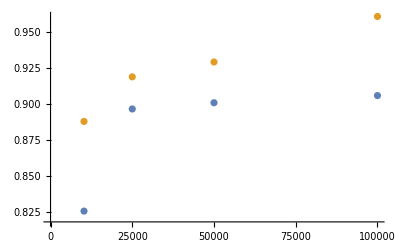

```mathematica
ListPlot[{Transpose[{datasize⟦2;;⟧,exp33$gen5⟦2;;⟧}],Transpose[{datasize⟦2;;⟧,exp54$gen5⟦2;;⟧}]}]
```

```mathematica
s1=a1+a2-a3;
s2=a2+a3-2a1;
s3=a3+3a1-a2;
s1^3+s2^3+s3^3-3s1 s2 s3//Expand
%//FullSimplify//FullSimplify
s1^3//Expand
s2^3//Expand
s3^3//Expand
-3s1 s2 s3//Expand
```

38 a1^3-9 a1^2 a2-6 a1 a2^2+4 a2^3+15 a1^2 a3-24 a1 a2 a3+6 a1 a3^2+4 a3^3

(2 a1+a2+a3) (19 a1^2-2 a1 (7 a2+a3)+4 (a2^2-a2 a3+a3^2))

a1^3+3 a1^2 a2+3 a1 a2^2+a2^3-3 a1^2 a3-6 a1 a2 a3-3 a2^2 a3+3 a1 a3^2+3 a2 a3^2-a3^3

-8 a1^3+12 a1^2 a2-6 a1 a2^2+a2^3+12 a1^2 a3-12 a1 a2 a3+3 a2^2 a3-6 a1 a3^2+3 a2 a3^2+a3^3

27 a1^3-27 a1^2 a2+9 a1 a2^2-a2^3+27 a1^2 a3-18 a1 a2 a3+3 a2^2 a3+9 a1 a3^2-3 a2 a3^2+a3^3

18 a1^3+3 a1^2 a2-12 a1 a2^2+3 a2^3-21 a1^2 a3+12 a1 a2 a3-3 a2^2 a3-3 a2 a3^2+3 a3^3

```mathematica
(x+y+z)(x^2+y^2+z^2-x y-y z-z x)//Expand
```

x^3+y^3-3 x y z+z^3

```mathematica
10 a^4-400 a^3+3994 a^2+120a//FullSimplify
```

2 (-20+a) a (-3+5 (-20+a) a)

### new experiments

#### new experiment 1 (5 2 20 4)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
new1$128$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new1/exp_new1_128_predictions.txt"];
new1$256$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new1/exp_new1_256_predictions.txt"];
new1$384$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new1/exp_new1_384_predictions.txt"];
new1$512$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new1/exp_new1_512_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
new1$128$result
new1$256$result
new1$384$result
new1$512$result
```

{0.,0.596,0.404}

{0.,0.028,0.972}

{0.,0.0243333,0.975667}

{0.,0.029,0.971}

```mathematica
testdata=TestData$FromFile["./Evaluation/new1/test_set_new1.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/new1/exp_new1_128_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
index=4;
testdata⟦index⟧
predictiondata⟦index⟧
PolySimplifyWithHint[{%%⟦1⟧,%},False,True]
PolySimplifyWithHint[{%%%⟦1⟧,%%%⟦2⟧},False,True]
```

{715-963 a[1]+431 a[1]^2-72 a[1]^3+4 a[1]^4,13-9 a[1]+a[1]^2}

{14-9 a[1]+a[1]^2}

1-5 s+4 s^2

3 s+4 s^2

```mathematica
data1={{128,0.404},{256,0.972},{384,0.97567},{512,0.971}};
```

#### new experiment 2 (split dataset)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
new2$128$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new2/exp_new2_128_predictions.txt"];
new2$256$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new2/exp_new2_256_predictions.txt"];
new2$384$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new2/exp_new2_384_predictions.txt"];
new2$512$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new2/exp_new2_512_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
new2$128$result
new2$256$result
new2$384$result
new2$512$result
```

{0.,0.625,0.375}

{0.,0.0273333,0.972667}

{0.,0.026,0.974}

{0.,0.0246667,0.975333}

```mathematica
data1={{128,0.404},{256,0.972},{384,0.97567},{512,0.971}};
data2={{128,0.375},{256,0.9727},{384,0.974},{512,0.97533}};
```

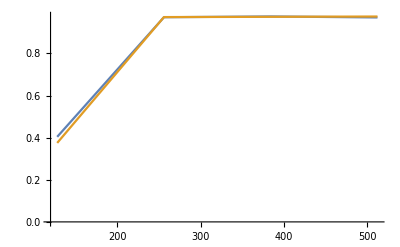

```mathematica
ListLinePlot[{data1,data2}]
```

```mathematica
?BarChart
```

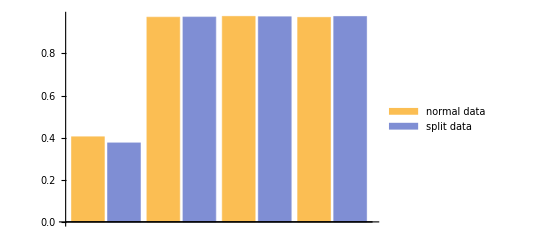

BarChart::ldata: {{{128,0.404},{256,0.972},{384,0.97567},{512,0.971}},{{128,0.375},{256,0.9727},{384,0.974},{512,0.97533}}} is not a valid dataset or list of datasets.

BarChart[{{{128,0.404},{256,0.972},{384,0.97567},{512,0.971}},{{128,0.375},{256,0.9727},{384,0.974},{512,0.97533}}}]

```mathematica
data1={{128,0.404},{256,0.972},{384,0.97567},{512,0.971}};
data2={{128,0.375},{256,0.9727},{384,0.974},{512,0.97533}};
data = {{0.404,0.375},{0.972,0.9727},{0.97567,0.974},{0.971,0.97533}};
BarChart[data,ChartLegends->{"normal data","split data"},BarSpacing->0.1]
```

#### Finetuning new1, new2 on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result$new1 = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_predictions.txt",False,True];
result$new2= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

```mathematica
result$new1
result$new2
```

{0.,0.943333,0.0566667}

{0.,0.937667,0.0623333}

```mathematica
result$new1$2560[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_2560_train1_predictions.txt",False,True];
result$new1$2560[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_2560_train2_predictions.txt",False,True];
result$new1$2560[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_2560_train3_predictions.txt",False,True];
Table[result$new1$2560[i]⟦3⟧,{i,3}]//Mean
result$new2$2560[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_2560_train1_predictions.txt",False,True];
result$new2$2560[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_2560_train2_predictions.txt",False,True];
result$new2$2560[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_2560_train3_predictions.txt",False,True];
Table[result$new2$2560[i]⟦3⟧,{i,3}]//Mean
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

0.543556

JaehaFormat$Parser failure : tail=!={}

0.635

```mathematica
result$new1$5120[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_5120_train1_predictions.txt",False,True];
result$new1$5120[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_5120_train2_predictions.txt",False,True];
result$new1$5120[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_5120_train3_predictions.txt",False,True];
Table[result$new1$5120[i]⟦3⟧,{i,3}]//Mean
result$new2$5120[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_5120_train1_predictions.txt",False,True];
result$new2$5120[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_5120_train2_predictions.txt",False,True];
result$new2$5120[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_5120_train3_predictions.txt",False,True];
Table[result$new2$5120[i]⟦3⟧,{i,3}]//Mean
```

0.763889

0.848444

```mathematica
result$new1$10240[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_10240_train1_predictions.txt",False,True];
result$new1$10240[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_10240_train2_predictions.txt",False,True];
result$new1$10240[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_10240_train3_predictions.txt",False,True];
Table[result$new1$10240[i]⟦3⟧,{i,3}]//Mean
result$new2$10240[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_10240_train1_predictions.txt",False,True];
result$new2$10240[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_10240_train2_predictions.txt",False,True];
result$new2$10240[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_10240_train3_predictions.txt",False,True];
Table[result$new2$10240[i]⟦3⟧,{i,3}]//Mean
```

0.826667

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

0.904778

```mathematica
result$new1$25k[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_25k_train1_predictions.txt",False,True];
result$new1$25k[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_25k_train2_predictions.txt",False,True];
result$new1$25k[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_25k_train3_predictions.txt",False,True];
Table[result$new1$25k[i]⟦3⟧,{i,3}]//Mean
result$new2$25k[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_25k_train1_predictions.txt",False,True];
result$new2$25k[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_25k_train2_predictions.txt",False,True];
result$new2$25k[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_25k_train3_predictions.txt",False,True];
Table[result$new2$25k[i]⟦3⟧,{i,3}]//Mean
```

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

0.869111

JFP$ReadN wrong : can't read term from {}

0.910444

```mathematica
result$new1$50k[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_50k_train1_predictions.txt",False,True];
result$new1$50k[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_50k_train2_predictions.txt",False,True];
result$new1$50k[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_50k_train3_predictions.txt",False,True];
Table[result$new1$50k[i]⟦3⟧,{i,3}]//Mean
result$new2$50k[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_50k_train1_predictions.txt",False,True];
result$new2$50k[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_50k_train2_predictions.txt",False,True];
result$new2$50k[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_50k_train3_predictions.txt",False,True];
Table[result$new2$50k[i]⟦3⟧,{i,3}]//Mean
```

0.901222

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

0.931

```mathematica
new1$2560=Table[{2560,result$new1$2560[i]⟦3⟧},{i,3}]
new1$5120=Table[{5120,result$new1$5120[i]⟦3⟧},{i,3}]
new1$10240=Table[{10240,result$new1$10240[i]⟦3⟧},{i,3}]
new1$25k=Table[{25000,result$new1$25k[i]⟦3⟧},{i,3}]
new1$50k=Table[{50000,result$new1$50k[i]⟦3⟧},{i,3}]
new1$total=new1$2560~Join~new1$5120~Join~new1$10240~Join~new1$25k~Join~new1$50k;
```

{{2560,0.533333},{2560,0.544667},{2560,0.552667}}

{{5120,0.761},{5120,0.731667},{5120,0.799}}

{{10240,0.817667},{10240,0.838667},{10240,0.823667}}

{{25000,0.874667},{25000,0.875},{25000,0.857667}}

{{50000,0.891333},{50000,0.901333},{50000,0.911}}

```mathematica
new2$2560=Table[{2560,result$new2$2560[i]⟦3⟧},{i,3}]
new2$5120=Table[{5120,result$new2$5120[i]⟦3⟧},{i,3}]
new2$10240=Table[{10240,result$new2$10240[i]⟦3⟧},{i,3}]
new2$25k=Table[{25000,result$new2$25k[i]⟦3⟧},{i,3}]
new2$50k=Table[{50000,result$new2$50k[i]⟦3⟧},{i,3}]
new2$total=new2$2560~Join~new2$5120~Join~new2$10240~Join~new2$25k~Join~new2$50k;
```

{{2560,0.543333},{2560,0.703333},{2560,0.658333}}

{{5120,0.829667},{5120,0.863667},{5120,0.852}}

{{10240,0.914667},{10240,0.900667},{10240,0.899}}

{{25000,0.913667},{25000,0.895667},{25000,0.922}}

{{50000,0.932667},{50000,0.926333},{50000,0.934}}

```mathematica
groupedData$new1=GroupBy[new1$total,First->Last]
groupedData$new2=GroupBy[new2$total,First->Last]
meanAndVariance$new1={#,Mean[groupedData$new1[#]],Variance[groupedData$new1[#]]}&/@Keys[groupedData$new1];
meanAndVariance$new2={#,Mean[groupedData$new2[#]],Variance[groupedData$new2[#]]}&/@Keys[groupedData$new2];
meanData$new1=meanAndVariance$new1[[All,{1,2}]];
errorBars$new1=meanAndVariance$new1[[All,3]];
meanData$new2=meanAndVariance$new2[[All,{1,2}]];
errorBars$new2=meanAndVariance$new2[[All,3]];
```

<|2560→{0.533333,0.544667,0.552667},5120→{0.761,0.731667,0.799},10240→{0.817667,0.838667,0.823667},25000→{0.874667,0.875,0.857667},50000→{0.891333,0.901333,0.911}|>

<|2560→{0.543333,0.703333,0.658333},5120→{0.829667,0.863667,0.852},10240→{0.914667,0.900667,0.899},25000→{0.913667,0.895667,0.922},50000→{0.932667,0.926333,0.934}|>

```mathematica
errorBar[{x_,y_},err_]:={Line[{{x,y-err},{x,y+err}}],(*Vertical error bar*)Line[{{x-0.05,y-err},{x+0.05,y-err}}],(*Bottom cap*)Line[{{x-0.05,y+err},{x+0.05,y+err}}]  (*Top cap*)};
```

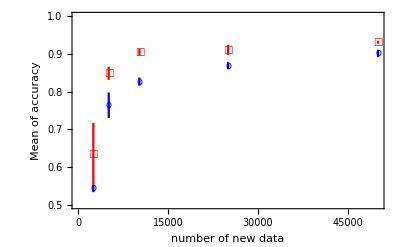

```mathematica
Needs["ErrorBarPlots`"];
plot1=ErrorListPlot[Thread[{meanData$new1,ErrorBar[Sqrt[#]]&/@errorBars$new1}],PlotMarkers->{"o",10},PlotStyle->Blue,PlotLegends->"based on normal data"];
plot2=ErrorListPlot[Thread[{meanData$new2,ErrorBar[Sqrt[#]]&/@errorBars$new2}],PlotMarkers->{"□",10},PlotStyle->Red,PlotLegends->"based on split data"];

Show[plot1,plot2,Frame->True,FrameLabel->{"number of new data","Mean of accuracy"},PlotRange->{{0,50000},{0.5,1.0}},ScalingFunctions->{"Log10",None}]
```

#### (test_new1 & train_new2 duplication test)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
TrainData$FromFile[filename_]:=Module[{data},data=(DeleteCases[#1,""]&)[StringSplit[Import[filename],"\n"|"?"]];data=data⟦1;;-2;;2⟧;data=(DeleteCases[#1,""]&)[StringSplit[data,"$"]];data=data/.str_String:>JF$Parser[str];data]
```

```mathematica
SetDirectory[NotebookDirectory[]]
new1$test = TestData$FromFile["./Evaluation/new1/test_set_new1.txt"];
new2$train=TrainData$FromFile["../../dataset_storage/datasets/new2/train_set_new2_test.txt"];
```

/Users/jaeha/inequality/MMA_package

```mathematica
new2$train⟦7⟧
```

{192+1054 a[1]+1011 a[1]^2-322 a[1]^3+2687 a[1]^4-810 a[1]^5+910 a[1]^6+140 a[1]^7+5 a[1]^8}

```mathematica
dupcheck=Table[new1$test⟦i,1⟧,{i,Length[new1$test]}]~Join~Table[new2$train⟦i,1⟧,{i,Length[new2$train]}];
Length[dupcheck]
Length[DeleteDuplicates[dupcheck]]
```

{19-176 a[1]+716 a[1]^2-1594 a[1]^3+2158 a[1]^4-1180 a[1]^5+65 a[1]^6+70 a[1]^7+5 a[1]^8,-2+8 a[1]-18 a[1]^2+7 a[1]^3+a[1]^4}

```mathematica
?PredictionData$FromFile
```

#### Finetuning new1, new2 on gen7

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result$new1$gen7$constant = {0,0,0,0,0,0};
result$new1$gen7$linear ={0,0,0,0,0,0};
result$new1$gen7$quadratic ={0,0,0,0,0,0};
result$new1$gen7$cubic={0,0,0,0,0,0};
```

```mathematica
(* without training *)
```

```mathematica
result$new1$gen7$constant⟦1⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦1⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦1⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦1⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_cube_predictions.txt",False,True]
```

{0.,0.444667,0.555333}

{0.,1.,0.}

{0.,1.,0.}

{0.,1.,0.}

```mathematica
(* with 2560 training *)
```

```mathematica
result$new1$gen7$constant⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_2560_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_2560_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_2560_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦2⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_2560_cube_predictions.txt",False,True]
```

{0.,0.166667,0.833333}

{0.,0.995,0.005}

{0.,1.,0.}

Part::take: Cannot take positions 2 through -1 in {}.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{}⟦2;;-1;;2⟧,$].

JFP$Read wrong : can't read term from {}

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{}⟦2;;-1;;2⟧,False].

Set::shape: Lists {coeff$78147593} and {} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

$Aborted

```mathematica
(* with 5120 training *)
```

```mathematica
result$new1$gen7$constant⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_5120_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_5120_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_5120_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦3⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_5120_cube_predictions.txt",False,True]
```

{0.,0.129667,0.870333}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

{0.,0.994333,0.00566667}

{0.,0.996667,0.00333333}

{0.,1.,0.}

```mathematica
(* with 10240 training *)
```

```mathematica
result$new1$gen7$constant⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_10240_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_10240_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_10240_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦4⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_10240_cube_predictions.txt",False,True]
```

{0.,0.0893333,0.910667}

{0.,0.990667,0.00933333}

{0.,0.998333,0.00166667}

{0.,0.992,0.008}

```mathematica
(* with 25k training *)
```

```mathematica
result$new1$gen7$constant⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_25k_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_25k_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_25k_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦5⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_25k_cube_predictions.txt",False,True]
```

{0.,0.09,0.91}

{0.,0.996667,0.00333333}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

{0.,0.999667,0.000333333}

{0.,1.,0.}

```mathematica
(* with 50k training *)
```

```mathematica
result$new1$gen7$constant⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_50k_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_50k_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_50k_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦6⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_50k_cube_predictions.txt",False,True]
```

{0.,0.0756667,0.924333}

JFP$ReadN wrong : can't read term from {}

{0.,0.999667,0.000333333}

{0.,1.,0.}

JFP$Read wrong : can't read term from {}

{0.,0.999333,0.000666667}

#### Finetuning new1, new2 on gen8

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result$new1$gen8$constant = {0,0,0,0,0,0};
result$new1$gen8$linear ={0,0,0,0,0,0};
result$new1$gen8$quadratic ={0,0,0,0,0,0};
result$new1$gen8$cubic={0,0,0,0,0,0};
```

```mathematica
(* with 2560 training *)
```

```mathematica
result$new1$gen8$constant⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_2560_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_2560_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_2560_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦2⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_2560_cube_predictions.txt",False,True]
```

{0.,0.574333,0.425667}

{0.,0.733667,0.266333}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

{0.,0.991,0.009}

JFP$Read wrong : can't read term from {}

{0.,0.993,0.007}

```mathematica
(* with 5120 training *)
```

```mathematica
result$new1$gen8$constant⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_5120_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_5120_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_5120_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦3⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_5120_cube_predictions.txt",False,True]
```

JFP$Read wrong : can't read term from {}

{0.,0.509333,0.490667}

{0.,0.666667,0.333333}

{0.,0.991333,0.00866667}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.,0.993667,0.00633333}

```mathematica
(* with 10240 training *)
```

```mathematica
result$new1$gen8$constant⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_10240_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_10240_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_10240_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦4⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_10240_cube_predictions.txt",False,True]
```

JFP$Read wrong : can't read term from {}

{0.,0.535667,0.464333}

JFP$ReadN wrong : can't read term from {}

{0.,0.574333,0.425667}

{0.,0.992333,0.00766667}

{0.,0.985667,0.0143333}

```mathematica
(* with 25k training *)
```

```mathematica
result$new1$gen8$constant⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_25k_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_25k_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_25k_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦5⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_25k_cube_predictions.txt",False,True]
```

{0.,0.549333,0.450667}

{0.,0.444333,0.555667}

JFP$Read wrong : can't read term from {}

{0.,0.998667,0.00133333}

JaehaFormat$Parser failure : tail=!={}

{0.,0.990667,0.00933333}

```mathematica
(* with 50k training *)
```

```mathematica
result$new1$gen8$constant⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_50k_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_50k_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_50k_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦6⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_50k_cube_predictions.txt",False,True]
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.,0.519,0.481}

{0.,0.389,0.611}

{0.,0.992,0.008}

{0.,0.998,0.002}

#### train on gen8 and test on constant, linear, quadratic, cubic

```mathematica
result$gen8$constant= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_gen8_512_constant_predictions.txt",False,True]
result$gen8$linear= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_gen8_512_linear_predictions.txt",False,True]
result$gen8$quadratic = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_gen8_512_quadratic_predictions.txt",False,True]
result$gen8$cubic= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_gen8_512_cube_predictions.txt",False,True]
```

JaehaFormat$Parser failure : tail=!={}

{0.,0.594667,0.405333}

JFP$ReadN wrong : can't read term from {}

{0.,0.150333,0.849667}

{0.,0.995,0.005}

{0.,0.999333,0.000666667}

#### new experiment 3 (5 2 20 4 without constraint)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result$l4$512=EvaluateSimplificationResult["./Evaluation/new3/test_set_new3.txt","./Evaluation/new3/new3_l4_512_predictions.txt"];
result$l4$768=EvaluateSimplificationResult["./Evaluation/new3/test_set_new3.txt","./Evaluation/new3/new3_l4_768_2_predictions.txt"];
result$l5$512=EvaluateSimplificationResult["./Evaluation/new3/test_set_new3.txt","./Evaluation/new3/new3_l5_512_2_predictions.txt"];
result$l5$768=EvaluateSimplificationResult["./Evaluation/new3/test_set_new3.txt","./Evaluation/new3/new3_l5_768_2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
result$l4$512
result$l4$768
result$l5$512
result$l5$768
```

{0.,0.247333,0.752667}

{0.,0.244333,0.755667}

{0.,0.818667,0.181333}

{0.,0.245667,0.754333}

```mathematica
testdata=TestData$FromFile["./Evaluation/new1/test_set_new1.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/new1/exp_new1_128_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
index=4;
testdata⟦index⟧
predictiondata⟦index⟧
PolySimplifyWithHint[{%%⟦1⟧,%},False,True]
PolySimplifyWithHint[{%%%⟦1⟧,%%%⟦2⟧},False,True]
```

{715-963 a[1]+431 a[1]^2-72 a[1]^3+4 a[1]^4,13-9 a[1]+a[1]^2}

{14-9 a[1]+a[1]^2}

1-5 s+4 s^2

3 s+4 s^2

```mathematica
data1={{128,0.404},{256,0.972},{384,0.97567},{512,0.971}};
```

### 2-language experiment

#### 2languages exp

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_40000_1_on_40000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_80000__on_40000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_80000__best_80000__on_40000_1.txt"]
(*EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_80000__best_80000__on_40000_2.txt"]*)
(*EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_40000_1_40000_2_on_40000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_2.txt","./Evaluation/2Lexp/prediction_set_80000__on_40000_2.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_2.txt","./Evaluation/2Lexp/prediction_set_40000_1_40000_2_on_40000_2.txt"]*)
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_40000_1_40000_2_best_40000__on_40000_1.txt"]
(*EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_2.txt","./Evaluation/2Lexp/prediction_set_40000_1_40000_2_best_40000__on_40000_2.txt"]*)
```

{0.,0.824333,0.175667}

JaehaFormat$Parser failure : tail=!={}

{0.,0.804,0.196}

{0.,0.802333,0.197667}

{0.,0.817667,0.182333}

```mathematica
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_200000__on_100000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_100000_1_on_100000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_100000_1_100000_2_100000__on_100000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_200000_1.txt","./Evaluation/2Lexp2/prediction_set_200000_1_on_200000_1.txt"]
```

{0.,0.105667,0.894333}

{0.,0.793333,0.206667}

{0.,0.121,0.879}

{0.,0.780333,0.219667}

#### scaling law for without constraint case

weight decay 0.01, learning_rate decay on, final token 10 ( turned out weight decay was actually 0.1 )

```mathematica
(* 1 language *)
```

```mathematica
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_40000_1_on_40000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_100000_1_on_100000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_200000_1.txt","./Evaluation/2Lexp2/prediction_set_200000_1_on_200000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_400000_1.txt","./Evaluation/2Lexp2/prediction_set_400000_1_on_400000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_800000_1.txt","./Evaluation/2Lexp2/prediction_set_800000_1_on_800000_1.txt"]
```

{0.,0.824333,0.175667}

{0.,0.793333,0.206667}

{0.,0.780333,0.219667}

JFP$Read wrong : can't read term from {}

{0.,0.787,0.213}

{0.,0.782667,0.217333}

```mathematica
(* 2 languages *)
```

```mathematica
result=
{
{40,EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_80000__on_40000_1.txt"]⟦3⟧},
{150,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_150000_.txt","./Evaluation/2Lexp2/prediction_set_150000__on_150000_.txt"]⟦3⟧},
{190,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_190000_.txt","./Evaluation/2Lexp2/prediction_set_190000__on_190000_.txt"]⟦3⟧},
{195,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_195000_.txt","./Evaluation/2Lexp2/prediction_set_195000__on_195000_.txt"]⟦3⟧},
{200,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_200000__on_100000_1.txt"]⟦3⟧},
{200.1,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_200100_.txt","./Evaluation/2Lexp2/prediction_set_200100__on_200100_.txt"]⟦3⟧},
{203.75,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_203750_.txt","./Evaluation/2Lexp2/prediction_set_203750__on_203750_.txt"]⟦3⟧},
{205,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_205000_.txt","./Evaluation/2Lexp2/prediction_set_205000__on_205000_.txt"]⟦3⟧},
{210,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_210000_.txt","./Evaluation/2Lexp2/prediction_set_210000__on_210000_.txt"]⟦3⟧},
{400,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_400000_.txt","./Evaluation/2Lexp2/prediction_set_400000__on_400000_.txt"]⟦3⟧}
}
```

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

{{40,0.196},{150,0.217667},{190,0.201},{200,0.894333},{200.1,0.908},{203.75,0.217},{400,0.215667}}

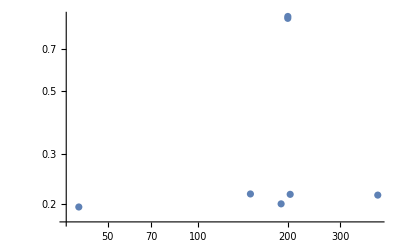

```mathematica
ListLogLogPlot[result⟦1;;7⟧]
```

weight decay 0.1, learning_rate decay on, final token 20000

```mathematica
(* 1 language *)
```

```mathematica
result2 =
{
{25,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_25003_1.txt","./Evaluation/2Lexp3/prediction_set_25003_1_on_25003_1.txt"]⟦3⟧},
{50,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_50003_1.txt","./Evaluation/2Lexp3/prediction_set_50003_1_on_50003_1.txt"]⟦3⟧},
{100,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_100003_1.txt","./Evaluation/2Lexp3/prediction_set_100003_1_on_100003_1.txt"]⟦3⟧},
{200,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_200003_1.txt","./Evaluation/2Lexp3/prediction_set_200003_1_on_200003_1.txt"]⟦3⟧},
{400,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_400003_1.txt","./Evaluation/2Lexp3/prediction_set_400003_1_on_400003_1.txt"]⟦3⟧}
}
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

{{25,0.155333},{50,0.186333},{100,0.22},{200,0.223},{400,0.226}}

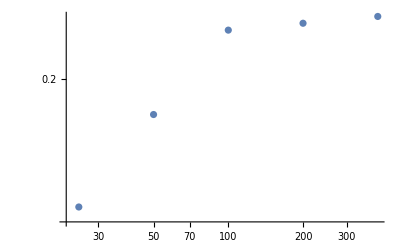

```mathematica
ListLogLogPlot[result2]
```

```mathematica
(* 2 languages *)
```

```mathematica
result=
{
{25,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_25003_.txt","./Evaluation/2Lexp3/prediction_set_25003__on_25003_.txt"]⟦3⟧},
{50,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_50003_.txt","./Evaluation/2Lexp3/prediction_set_50003__on_50003_.txt"]⟦3⟧},
{100,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_100003_.txt","./Evaluation/2Lexp3/prediction_set_100003__on_100003_.txt"]⟦3⟧},
{200,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_200003_.txt","./Evaluation/2Lexp3/prediction_set_200003__on_200003_.txt"]⟦3⟧},
{400,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_400003_.txt","./Evaluation/2Lexp3/prediction_set_400003__on_400003_.txt"]⟦3⟧}
}
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

{{25,0.443},{50,0.724333},{100,0.846333},{200,0.216333},{400,0.225333}}

weight decay 0.1, learning_rate decay on, final token 10000

```mathematica
(* 1 language *)
```

```mathematica
result3 =
{
{25,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_25004_1.txt","./Evaluation/2Lexp4/prediction_set_25004_1_on_25004_1.txt"]⟦3⟧},
{50,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_50004_1.txt","./Evaluation/2Lexp4/prediction_set_50004_1_on_50004_1.txt"]⟦3⟧},
{100,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_100004_1.txt","./Evaluation/2Lexp4/prediction_set_100004_1_on_100004_1.txt"]⟦3⟧},
{200,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_200004_1.txt","./Evaluation/2Lexp4/prediction_set_200004_1_on_200004_1.txt"]⟦3⟧},
{400,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_400004_1.txt","./Evaluation/2Lexp4/prediction_set_400004_1_on_400004_1.txt"]⟦3⟧}
}
```

JFP$Read wrong : can't read term from {}

{{25,0.151667},{50,0.520333},{100,0.214333},{200,0.221667},{400,0.215}}

```mathematica
(* turning off shuffle *)
```

```mathematica
EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_100005_1.txt","./Evaluation/2Lexp4/prediction_set_100005_1_on_100005_1.txt"]
```

{0.,0.76,0.24}

### multi-variable

#### 5 variables ( Exp 60 ) - (5, 3, 5, 3 ), 3 terms each ( 5var2 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* TestData$FromFile2 : only read question *)
```

```mathematica
testdata=TestData$FromFile2["./Evaluation/multi/test_set_5var2.txt"];
```

```mathematica
(* read model's prediction and split in & *)
```

```mathematica
predictiondata=PredictionData$FromFile3["./Evaluation/multi/multi_l4_512_5var2_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

```mathematica
predictiondata⟦1⟧
```

{-2 b[0]^2 b[1]-2 b[0] b[1] b[2]-2 b[1]^2 b[2],-a[1]^2 a[2]-a[0] a[3]^2-2 a[0]^2 a[4],-a[2] a[3]^2-2 a[0]^2 a[4],-3 a[1] a[3]^2,-2 a[0]^2 a[1]-4 a[1]^2 a[2],-2 a[0]^2 a[1]-2 a[0] a[1] a[2]-4 a[1]^2 a[2]}

```mathematica
index =324;
testdata⟦index⟧
predictiondata[[index,1]]/.{b[a_]:>predictiondata⟦index,a+2⟧}//Expand
(%-%%)===0
```

-60 a[0]^3 a[1]^6+40 a[0] a[1]^8-48 a[0]^4 a[1]^4 a[2]+80 a[0]^2 a[1]^6 a[2]-76 a[1]^7 a[2] a[3]-102 a[0] a[1]^6 a[2] a[4]-90 a[0]^3 a[1]^3 a[2]^2 a[4]+60 a[0] a[1]^5 a[2]^2 a[4]-36 a[0]^4 a[1] a[2]^3 a[4]+60 a[0]^2 a[1]^3 a[2]^3 a[4]-114 a[1]^4 a[2]^3 a[3] a[4]+60 a[0] a[1]^6 a[4]^2+48 a[0]^2 a[1]^4 a[2] a[4]^2-108 a[0] a[1]^3 a[2]^3 a[4]^2-45 a[0]^3 a[2]^4 a[4]^2+45 a[0] a[1]^2 a[2]^4 a[4]^2-54 a[1] a[2]^5 a[3] a[4]^2+90 a[0] a[1]^3 a[2]^2 a[4]^3+36 a[0]^2 a[1] a[2]^3 a[4]^3-18 a[0] a[2]^5 a[4]^3+45 a[0] a[2]^4 a[4]^4

-240 a[0]^3 a[1]^6-400 a[0] a[1]^8-48 a[0]^2 a[1]^5 a[2] a[3]+256 a[1]^7 a[2] a[3]+36 a[0]^3 a[1]^4 a[2] a[4]-192 a[0] a[1]^6 a[2] a[4]-360 a[0]^3 a[1]^3 a[2]^2 a[4]-600 a[0] a[1]^5 a[2]^2 a[4]-36 a[0]^2 a[1]^2 a[2]^3 a[3] a[4]+384 a[1]^4 a[2]^3 a[3] a[4]-240 a[0] a[1]^6 a[4]^2+27 a[0]^3 a[1] a[2]^3 a[4]^2-288 a[0] a[1]^3 a[2]^3 a[4]^2-135 a[0]^3 a[2]^4 a[4]^2-225 a[0] a[1]^2 a[2]^4 a[4]^2-48 a[0] a[1]^4 a[2] a[3] a[4]^2+144 a[1] a[2]^5 a[3] a[4]^2+36 a[0]^2 a[1]^3 a[2] a[4]^3-360 a[0] a[1]^3 a[2]^2 a[4]^3-108 a[0] a[2]^5 a[4]^3-36 a[0] a[1] a[2]^3 a[3] a[4]^3+27 a[0]^2 a[2]^3 a[4]^4-135 a[0] a[2]^4 a[4]^4

False

```mathematica
simplification$result = Table[testdata[[i]]===(predictiondata[[i,1]]/.{b[a_]:>predictiondata⟦i,a+2⟧}//Expand),{i,1,Length@predictiondata}];
```

Part::partw: Part 6 of {5 b[0]^2 b[1]-5 b[1]^2 b[3]-b[2]^2 b[4],3 a[1] a[3]^2+5 a[2] a[3]^2+4 a[1] a[3] a[4],-a[1]^3+4 a[0] a[3]^2+5 a[2] a[3]^2,2 a[0] a[1]^2+3 a[0] a[2] a[4]+5 a[0] a[3] a[4],-4 a[0] a[2]^2+5 a[0] a[3]^2-a[0] a[2] a[4]} does not exist.

```mathematica
Count[simplification$result,False]
Count[simplification$result,True]
```

2991

9

#### 5 variables ( Exp 61 ) - (5, 3, 5, 1 ), 9, 5 terms each ( 5var3 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* TestData$FromFile2 : only read question *)
```

```mathematica
testdata=TestData$FromFile2["./Evaluation/multi/test_set_5var3.txt"];
```

```mathematica
(* read model's prediction and split in & *)
```

```mathematica
predictiondata=PredictionData$FromFile3["./Evaluation/multi/multi_l4_512_5var3_finetune_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

```mathematica
predictiondata⟦1⟧
```

{-5 b[0]^2 b[1]-b[0] b[1]^2-5 b[0]^2 b[2]-2 b[0] b[1] b[2]-5 b[1]^2 b[2]-b[0] b[2]^2-5 b[0]^2 b[3]-2 b[0] b[2] b[3]-2 b[0] b[3]^2,4 a[3]-a[4],-3 a[2],-2 a[4],a[0]+3 a[1]-4 a[2],-4 a[0]-3 a[1]-2 a[2]-5 a[3]-4 a[4]}

```mathematica
index =324;
testdata⟦index⟧
predictiondata[[index,1]]/.{b[a_]:>predictiondata⟦index,a+2⟧}//Expand
(%-%%)===0
```

15 a[0]^3+36 a[0]^2 a[1]-320 a[1]^3+92 a[0]^2 a[2]-112 a[0] a[1] a[2]+189 a[0] a[2]^2+40 a[1] a[2]^2-148 a[2]^3-12 a[0]^2 a[4]-40 a[0] a[2] a[4]+32 a[2]^2 a[4]

17 a[0]^3-40 a[0]^2 a[1]-320 a[1]^3+188 a[0]^2 a[2]-300 a[0] a[1] a[2]+713 a[0] a[2]^2-592 a[1] a[2]^2+908 a[2]^3

False

```mathematica
simplification$result = Table[testdata[[i]]===(predictiondata[[i,1]]/.{b[a_]:>predictiondata⟦i,a+2⟧}//Expand),{i,1,Length@predictiondata}];
```

```mathematica
Count[simplification$result,False]
Count[simplification$result,True]
```

3000

0

#### 5 variables ( Exp 62 ) - (5, 3, 5, 1 ), 10, 5 terms each ( 5var4 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* TestData$FromFile2 : only read question *)
```

```mathematica
testdata=TestData$FromFile2["./Evaluation/multi/test_set_5var4.txt"];
```

```mathematica
(* read model's prediction and split in & *)
```

```mathematica
predictiondata=PredictionData$FromFile3["./Evaluation/multi/multi_l4_512_5var4_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«18 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
predictiondata⟦1⟧
```

{-5 b[0]^3-5 b[0]^2 b[1]-5 b[0] b[1]^2-5 b[0] b[1] b[2]-5 b[1]^2 b[2]-3 b[0] b[2]^2-5 b[1]^2 b[3]-3 b[0] b[2] b[3]-5 b[1] b[2] b[3]-5 b[2]^2 b[4],-5 a[0]-a[1]-2 a[2]-5 a[3]-a[4],-5 a[0]-4 a[1]-a[2]+4 a[3]-2 a[4],-3 a[0]-2 a[1]-3 a[2]-5 a[3]-a[4],-4 a[0]-4 a[1]-a[2]-a[3]-a[4],False}

```mathematica
index =324;
testdata⟦index⟧
predictiondata[[index,1]]/.{b[a_]:>predictiondata⟦index,a+2⟧}//Expand
(%-%%)===0
```

15 a[0]^3-58 a[0]^2 a[1]-184 a[0] a[1]^2+495 a[1]^3-49 a[0]^2 a[2]+151 a[0] a[1] a[2]+109 a[1]^2 a[2]+38 a[0] a[2]^2-18 a[1] a[2]^2-4 a[2]^3-30 a[0]^2 a[3]+339 a[0] a[1] a[3]-945 a[1]^2 a[3]+55 a[0] a[2] a[3]-314 a[1] a[2] a[3]-25 a[2]^2 a[3]-91 a[0] a[3]^2+455 a[1] a[3]^2+91 a[2] a[3]^2+70 a[0]^2 a[4]+300 a[0] a[1] a[4]-1445 a[1]^2 a[4]-150 a[0] a[2] a[4]-275 a[1] a[2] a[4]+5 a[2]^2 a[4]-340 a[0] a[3] a[4]+1895 a[1] a[3] a[4]+315 a[2] a[3] a[4]-455 a[3]^2 a[4]-125 a[0] a[4]^2+1450 a[1] a[4]^2+175 a[2] a[4]^2-950 a[3] a[4]^2-500 a[4]^3

105 a[0]^3+765 a[0]^2 a[1]+1480 a[0] a[1]^2+820 a[1]^3+241 a[0]^2 a[2]+882 a[0] a[1] a[2]+694 a[1]^2 a[2]+129 a[0] a[2]^2+191 a[1] a[2]^2+17 a[2]^3+560 a[0]^2 a[3]+1780 a[0] a[1] a[3]+1220 a[1]^2 a[3]+492 a[0] a[2] a[3]+624 a[1] a[2] a[3]+76 a[2]^2 a[3]+435 a[0] a[3]^2+435 a[1] a[3]^2+87 a[2] a[3]^2+480 a[0]^2 a[4]+2085 a[0] a[1] a[4]+1870 a[1]^2 a[4]+620 a[0] a[2] a[4]+1065 a[1] a[2] a[4]+150 a[2]^2 a[4]+1535 a[0] a[3] a[4]+2195 a[1] a[3] a[4]+575 a[2] a[3] a[4]+435 a[3]^2 a[4]+1125 a[0] a[4]^2+1800 a[1] a[4]^2+475 a[2] a[4]^2+975 a[3] a[4]^2+750 a[4]^3

False

```mathematica
simplification$result = Table[testdata[[i]]===(predictiondata[[i,1]]/.{b[a_]:>predictiondata⟦i,a+2⟧}//Expand),{i,1,Length@predictiondata}];
```

Part::partw: Part 6 of {-5 b[0]^3-5 b[0] b[1]^2-5 b[0] b[1] b[2]-5 b[1]^2 b[2]-5 b[0] b[2]^2-5 b[1] b[2]^2-3 b[0] b[1] b[3]-5 b[0] b[2] b[3]-3 b[1] b[2] b[3]-5 b[0] b[1] b[4]+«1»,-4 a[0]+5 a[1]-4 a[2]-a[3]-3 a[4],-a[0]-5 a[1]-4 a[2]-a[3]-4 a[4],-3 a[0]-2 a[1]-5 a[2]-a[3]-4 a[4],False} does not exist.

Part::partw: Part 6 of {-4 b[0]^3-5 b[0]^2 b[1]-5 b[0] b[1]^2-4 b[1]^2 b[2]-4 b[0] b[2]^2-4 b[0]^2 b[3]-4 b[0] b[1] b[3]-4 b[1]^2 b[3]-4 b[0] b[2] b[3]-4 b[2]^2 b[3]+«1»,-5 a[0]-4 a[1]-4 a[2]-5 a[3]-a[4],-a[1]-3 a[2]-3 a[3]-3 a[4],-a[0]-3 a[1]-4 a[2]-a[3]-4 a[4],-4 a[0]-5 a[1]-4 a[2]-4 a[3]-a[4]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Count[simplification$result,False]
Count[simplification$result,True]
```

2996

4

#### 5 variables ( Exp 63 ) - (5, 3, 5, 1 ), 10, 5 terms each ( 5var4, l6 d768 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* TestData$FromFile2 : only read question *)
```

```mathematica
testdata=TestData$FromFile2["./Evaluation/multi/test_set_5var4.txt"];
```

```mathematica
(* read model's prediction and split in & *)
```

```mathematica
predictiondata=PredictionData$FromFile3["./Evaluation/multi/multi_l6_768_5var4_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}